# Thesis Plots

## Intialisation

```mathematica
setChapDir[name_]:=SetDirectory[FileNameJoin[{NotebookDirectory[],"Figures",name,"PlotData"}]]
Needs["ErrorBarPlots`"]
SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16,FontColor->Black},ImageSize->600,Frame->True,Axes->False];
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
SetOptions[Histogram,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
SetOptions[DateListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
SetOptions[ErrorListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->16},ImageSize->600,Frame->True,Axes->False];
absq[z_]:=ComplexExpand[z Conjugate[z]]
```

myGridDivision can be used to set some kind of style for major and minor grids

```mathematica
myGridDivision[{min_,max_},{major_,majorStyle_},{minor_,minorStyle_}]:=Function[divisions,Join[{#,majorStyle}&/@divisions[[1]],{#,minorStyle}&/@Complement[Flatten[#[[2]]],#[[1]]]&@divisions]][FindDivisions[{min,max},{major,minor}]]
Colours=Darker[#]&/@{Red,Green,Blue,Black,Purple,Yellow,Brown,Orange,Pink,Gray,Cyan,Magenta};
```

```mathematica
plotExport[plot_,name_]:=Export["../"<>name<>".pdf",plot]
dataExport[plot_,name_]:=Module[{data},
data=Cases[plot,Line[data_]:>data,-4,1][[1]];
Export["PlotData/"<>name<>".csv",data,"CSV"]
]
multiDataExport[plot_,name_]:=Module[{data},
data=Cases[First@plot,Line[data_]:>N[data],-4];
Export["PlotData/"<>name<>IntegerString[#2,10,3]<>".csv",#,"CSV"]&~MapIndexed~data
]
```

```mathematica
?IntegerString
```

IntegerString[n] gives a string consisting of the decimal digits in the integer n. 
IntegerString[n,b] gives a string consisting of the base-b digits in the integer n. 
IntegerString[n,b,len] pads the string on the left with zero digits to give a string of length len. 
IntegerString[n,MixedRadix[blist]] uses the mixed radix with a list of bases blist.
IntegerString[n,numsys] gives the numeral form of n based on the numeric system defined by numsys.

## Chapter 1

## Chapter 2

## Chapter 3

This section focuses on the experimental setup

```mathematica
setChapDir["Chapter3"]
```

/media/Storage/Dropbox/PhDWork/Thesis/Figures/Chapter3/PlotData

## Muquans Spectra

### Sat. Spec Signal

```mathematica
satspec = Import["satspec.csv"];
```

The 3,4 Rb85 crossover is at 384.2291813694837 THz. All frequencies will be shifted relative to that, in units of MHz

```mathematica
satdata={(#⟦1⟧-384.2291813694837)*10^6,#⟦2⟧+1.18}&/@satspec;
```

```mathematica
satspecPlot=ListPlot[satdata,GridLines->{myGridDivision[{-1500,1000},{5,GrayLevel[.1]},{10,{Dashed,GrayLevel[.8]}}],myGridDivision[{-2,4},{10,GrayLevel[.1]},{10,{Dashed,GrayLevel[.8]}}]},FrameStyle->Thick,FrameLabel->{"Detuning from^85Rb F=3 → F'=3,4 crossover (MHz)","abs. signal (arb. units)"}]
```

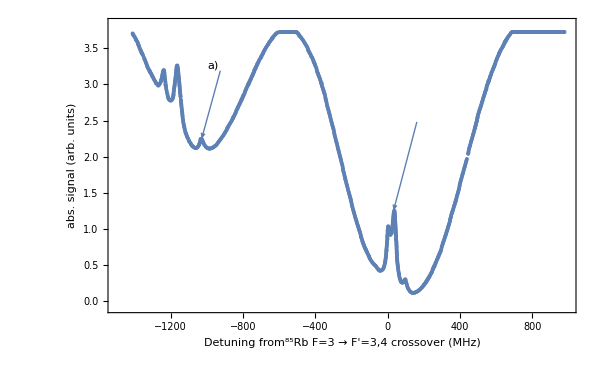

```mathematica
plotExport[satspecPlot,"sat_spec"]
```

### Error Signal

### Slave 0 Error

### Slave 1 Error

## Chapter 4 - MOT

## Chapter 5 - State Prep

## Chapter 6 - Interferometer

```mathematica
SetDirectory["~/Dropbox/PhDWork/Thesis/Figures/Chapter6"]
```

/media/Storage/Dropbox/PhDWork/Thesis/Figures/Chapter6

Key Functions

These functions are used to define the propagator for a two-level atom. This is a simplified model for the Raman transition

```mathematica
a[Ω_,δ_]:=√(Ω^2+δ^2)
prop[ω_,t_,a_,Ω_,ϕ_,δ_]:=({{ⅇ^(ⅈ (ω t)/2)( Cos[1/2 t a]-ⅈ δ/a Sin[1/2 t a]), - ⅇ^(ⅈ(ω t)/2)(ⅈ Ω ⅇ^(ⅈ ϕ)Sin[1/2 t a])/a}, {-ⅇ^(-ⅈ (ω t)/2)(ⅈ Ω ⅇ^(-ⅈ ϕ)Sin[1/2 t a])/a, ⅇ^(-ⅈ (ω t)/2)( Cos[1/2 t a]+ ⅈ δ/a Sin[1/2 t a])}})
prop[ω0_,ω_,δDopp_,Ω_,t0_,τ_,ϕ_]:=prop[ω+δDopp,τ,a[Ω,ω+δDopp-ω0],Ω,ϕ+ ω t0,ω-ω0+δDopp]
free[ω0_,T_]:={{ⅇ^(ⅈ ω0 T/2),0},{0,ⅇ^(-ⅈ ω0 T/2)}}
```

The fringe is then obtained from successive products of this operator and the free evolution

```mathematica
fringe[{Ω1_,τ1_,δ1_,ϕ1_} ,{Ω2_,τ2_,δ2_,ϕ2_},{Ω3_,τ3_,δ3_,ϕ3_},T1_,T2_,init_:{1,0}]:=prop[ω0,ω,δ3,Ω3,T2+τ2+T1+τ1,τ3,ϕ3].free[ω0,T2].prop[ω0,ω,δ2,Ω2,T1+τ1,τ2,ϕ2].free[ω0,T1].prop[ω0,ω,δ1,Ω1,0,τ1,ϕ1].init
```

Raman Optics

## Fringe Contrast vs Beam Width

I’ll consider the effects of the beam width on the contrast by assuming a Gaussian distribution of atoms. The total contrast is a convolution of this with the fringe pattern for a single atom. Without loss of generality, I can set the peak intensity to give the correct pulse area.

```mathematica
Ω[r_,Ω0_:Ω0]:=Ω0 Exp[-2 r^2/r0^2]
transverseFringe[T_]=1/(√(2π)σ)Exp[-rinit^2/(2 σ^2)]absq[fringe[{Ω[rinit,π/2],1,0,0},{Ω[rinit+u T-1/2 g T^2,π],1,0,ϕ},{Ω[rinit+u T-g T^2,π/2],1,0,0},T,T]]⟦1⟧;
```

```mathematica
contrast[cloud_,beam_]:=NIntegrate[Subtract@@(transverseFringe[25 10^-3]//.{ϕ->{0,π/2},u->0,ω->ω0,ω0->0,g->9.81,r0-> beam 10^-3,σ-> cloud 10^-3,rinit->r}),{r,-0.1,0.1},Method->"Trapezoidal"]
```

NIntegrate::inumri: The integrand -100 «2» (Cos[1/4 Power[«2»] π]^2 Cos[1/2 Power[«2»] π]^2 Cos[1/4 Power[«2»] π]^2+1. Cos[1/4 Power[«2»] π]^2 Sin[1/4 Power[«2»] π]^2 Sin[1/2 Power[«2»] π]^2-(«1»)/(«1»)-(«1»)/(«1»)+1. Cos[1/2 «1» π]^2 Sin[«1»]^2 Sin[1/4 Power[«2»] π]^2+1. Cos[1/4 Power[«2»] π]^2 Sin[1/2 Power[«2»] π]^2 Sin[1/4 Power[«2»] π]^2)+«1» has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-∞,∞}}.

NIntegrate::inumri: The integrand -79.7885 ⅇ^(-20000. r^2) (0.+«12»+(«24» «5» («1»)^2)/(√(0.+«1») √(«1») («1»))+(24.3523 ⅇ^(«1») Cos[1/2 Power[«2»]]^2 Sin[1/2 Power[«2»]]^2 Sin[1/2 Power[«2»]]^2)/((0.+Power[«2»] Power[«2»]) (0.+1/4 Power[«2»] Power[«2»])))+79.7885 ⅇ^(-20000. «1») (0.+«13») has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{-∞,∞}}.

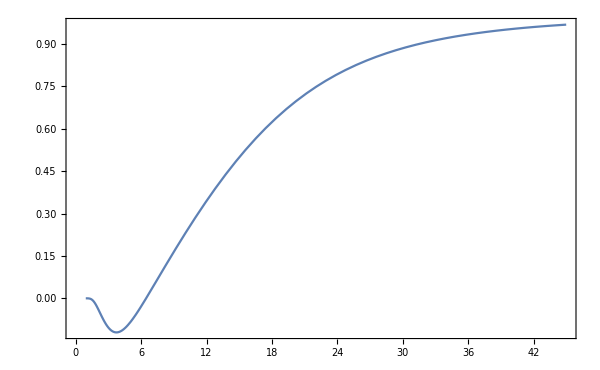

```mathematica
Plot[contrast[5,b],{b,0,45}]
```

```mathematica
dataExport[%82,"fringeContrast"]
```

../fringeContrast.txt

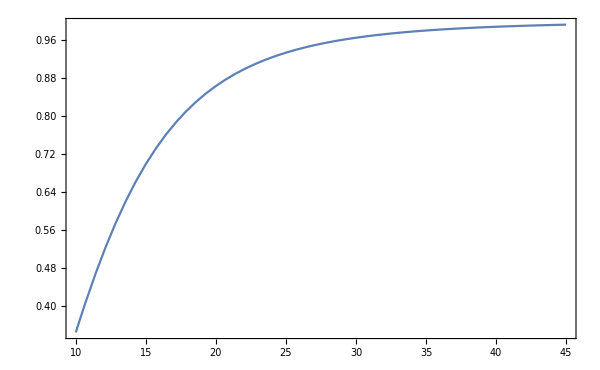

```mathematica
Plot[contrast[2.5,b],{b,10,45}]
```

## Phase Noise

Now I’ll consider the effects of phase noise on the fringe pattern. For this, I’ll generate fringes which have a random phase component at each pulse and take their average

```mathematica
absq[fringe[{1,π/2,0,ϕ1} ,{1,π,0,ϕ2},{1,π/2,0,ϕ3},T,T]//.{ω->0,ω0->0}]⟦1⟧//FullSimplify
```

Cos[1/2 (ϕ1-2 ϕ2+ϕ3)]^2

Assuming each pulse has an uncorrelated, random phase, I can use Gaussian propagation of error to combine them. I’ll set ϕ1=ϕ3=0, and  the variance on this phase is σ_ϕ. I can write the fringe pattern as

```mathematica
Cos[ϕ2 + δϕ]^2
```

Where δϕ ~N(0, 6(σ^2)_ϕ) is the random component. The contrast, i.e. the maximum value minus the minimum value is

```mathematica
cont[b_]=Subtract@@(TrigExpand[Cos[a+b]^2]/.{a->{0,π/2}})
```

Cos[b]^2-Sin[b]^2

```mathematica
Cos[b]^2-Sin[b]^2//FullSimplify
```

Cos[2 b]

The mean of this is given by E[c[x]] = ∫c[x]p[x], where p[x] is the Gaussian pdf

```mathematica
Integrate[cont[b] 1/(√(2π)σ)Exp[-b^2/(2 σ^2)],{b,-∞,∞},Assumptions->{σ∈Reals,σ>0}]
```

```mathematica
2. π/50
```

0.125664

```mathematica
Exp[-2 σ^2]/.σ->√6 0.12
```

0.841306

Now, I’ll plot this average contrast with the phase in units of λ (1 wavelength spans a phase of 2π radians)

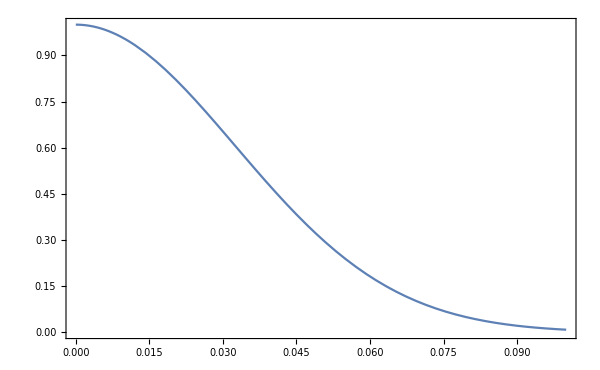

```mathematica
Plot[ⅇ^(-2 σ^2)/.σ->2π √6 s,{s,0,0.1}]
```

```mathematica
ⅇ^(-2 σ^2)/.σ->2π √6 s/.s->0.05
```

0.305944

```mathematica
dataExport[%108, "phaseNoise"]
```

phaseNoise.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["phaseNoise.csv"]]]
```

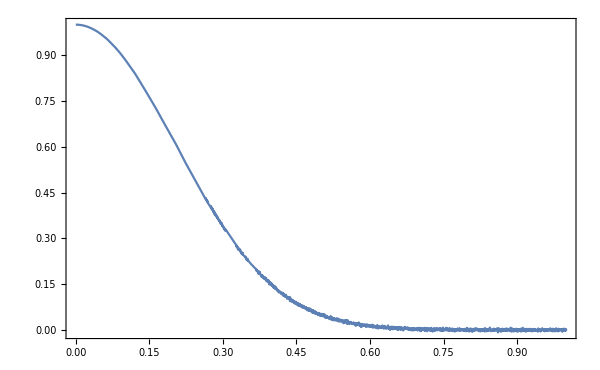

```mathematica
Plot[Mean[cont[b]]/.b->RandomVariate[NormalDistribution[0,√6 s],100000],{s,0,1}]
```

## Ray Tracing Initialization

#### Units

```mathematica
mm=10^-3;
cm=10^-2;
µm=um=10^-6;
nm=10^-9;
```

#### Load Packages

```mathematica
Needs["Optics`Gaussian`"]
```

plot::shdw: Symbol plot appears in multiple contexts {Optics`Gaussian`,Global`}; definitions in context Optics`Gaussian` may shadow or be shadowed by other definitions.

```mathematica
Needs["Optics`RayTracing`"]
```

```mathematica
Needs["Optics`LensDefinitions`"]
```

#### Ray bundles

This is a ray fan starting at the origin and filling the 1/e points of the effective gaussian beam

```mathematica
initialBundle[θmax_]:= With[{npts=30}, Table[Ray[0., 0. , θ, 1.], {θ,-θmax,θmax,(2θmax)/(npts-1)}]];
```

This turns off warning messages for rays leaving or clipping the optical system

```mathematica
Off[RayTracing::lostray]
```

#### Wavelength

This is the wavelength of the Raman beams

```mathematica
$λ = 780nm;
```

This is the wavelength difference between the Raman beams that are separated in frequency by 6.8GHz

```mathematica
Δλ = (-($λ)^2)/c Δf/.{c->3*10^8, Δf->6.8*10^9};
```

#### Messages

```mathematica
Off[Solve::ratnz];
```

## Triplet Lens and Aspheric Lenses

Here we consider an optical system that will expand the beam to fill the triplet lens.  The C230260P-B mounted pair consists of a 352230-B (f = 4.51mm) and a 352260-B (f = 15.29mm), which is now superseded by 354260-B.  We use this in the reverse orientation to that shown below..

### Aspheric lenses

-Graphics-

```mathematica
15.29/4.51
```

3.39024

```mathematica
13*3.39
```

44.07

```mathematica
lens4:=Reversed[GelTech["352260"][$λ]];
lens5:=Geltech["352230"][$λ];
```

### Define optical systems

We want a Train[] object for the gaussian optics package, and a list of interfaces for ray-tracing.  The gaussian beam approximation only works with spherical surfaces, so use that approximation to the aspheric enses.

```mathematica
trainC230260P[p_]:=Train[Translation[p], SingletLens[R1,R2,TC1,N1]/.lens4, Translation[1.067mm], SingletLens[R1,R2,TC1,N1]/.lens5];
```

The expander is distance d0 from the fiber tip, the triplet is d1 from the back of the expander, and the end of the path is d2 from the back of the triplet.

```mathematica
opticsC230260PTriplet[d0_, d1_, d2_]:=Flatten[{
  Aspheric[{R1,k1,A4,A6,A8,A10,A12,A14,A16},{R2,k2,B4,B6,B8,B10,B12,B14,B16},TC1,N1,Dia][d0]/.lens4,
  Aspheric[{R1,k1,A4,A6,A8,A10,A12,A14,A16},{R2,k2,B4,B6,B8,B10,B12,B14,B16},TC1,N1,Dia][d0+(TC1/.lens4)+1.067mm]/.lens5,
  AirSpacedTriplet[R1,R2,R3,R4,R5,R6,TC1,TC2,TC3,gap1,gap2,N1,N2,N3,Dia][d0+(TC1/.lens4)+1.067mm+(TC1/.lens5)+d1]/.lens3,
  Interface[∞, d0 + (TC1/.lens4) + 1.067mm + (TC1/.lens5) + d1 + (TC1+TC2+TC3+gap1+gap2/.lens3) + d2, 1, 25mm]}];
```

### Focal length and principal planes

#### Triplet

```mathematica
trainTriplet=Train@(AirSpacedTripletLens[R1,R2,R3,R4,R5,R6,TC1,TC2,TC3,gap1,gap2,N1,N2,N3]/.gap1->1.674928mm)/.ICOS["CCM-Triplet"][$λ];
```

```mathematica
ppTriplet=PrincipalPlanes[H1,H2,F][trainTriplet]//First
```

{H1→-0.0125813,H2→-0.00821167,F→0.136039}

```mathematica
frontFocusTriplet=F+H1/.ppTriplet
```

0.123458

```mathematica
backFocusTriplet=F+H2/.ppTriplet
```

0.127828

#### f = 15.3mm lens

```mathematica
ppLens4=PrincipalPlanes[H1,H2,F][Train[SingletLens[R1,R2,TC1,N1]/.lens4]]//First
```

{H1→-0.00137961,H2→0.,F→0.0153701}

Location of focal points before and after the lens

```mathematica
frontFocusLens4=F+H1/.ppLens4
```

0.0139905

```mathematica
backFocusLens4=F+H2/.ppLens4
```

0.0153701

Turn the lens around and send in a collimated beam.  The lens is positioned so that its back surface is at 0.1m from the origin.  The orange line at 0.223434m  is the position of the focus predicted by the geometrical optics calculation above as frontFocusTriplet with respect to the lens surface on axis.  It’s clear that gives a very good indication of the focal point.

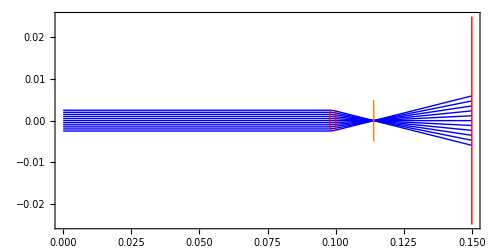

```mathematica
Block[
{d=100mm-TC1/.lens4,
optics=Flatten[{Aspheric[{R1,k1,A4,A6,A8,A10,A12,A14,A16},{R2,k2,B4,B6,B8,B10,B12,B14,B16},TC1,N1,Dia][d]/.Reversed[lens4],Interface[∞,150mm,1,25mm]}]},
g={RayPathGraphics[optics][Table[Ray[0,y,0,1],{y,-10mm,10mm,1/2 mm}],Blue], InterfaceGraphics[optics]};
Show[g,PlotRange->{{0,All},{-25mm,25mm}},PlotRangeClipping->True,Frame->True,AspectRatio->1/2,ImageSize->500,Epilog->{Orange,Line[{{100 mm+frontFocusLens4,-5mm},{100 mm+frontFocusLens4,5mm}}]}]]
```

Zoom in.  It’s clear that we want the first aspheric 13.9905 mm from the fiber tip

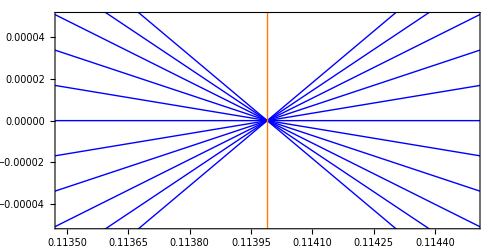

```mathematica
Block[{d=100mm-TC1/.lens4,optics=Flatten[{Aspheric[{R1,k1,A4,A6,A8,A10,A12,A14,A16},{R2,k2,B4,B6,B8,B10,B12,B14,B16},TC1,N1,Dia][d]/.Reversed[lens4],Interface[∞,150mm,1,25mm]}]},
g={RayPathGraphics[optics][Table[Ray[0,y,0,1],{y,-10mm,10mm,1/2 mm}],Blue], InterfaceGraphics[optics]};
Show[g,PlotRange->{0.1+0.0139905+0.0005*{-1,1},{-50µm,50µm}},PlotRangeClipping->True,Frame->True,AspectRatio->1/2,ImageSize->500,Epilog->{Orange,Line[{{100mm+frontFocusLens4,-5mm},{100mm+frontFocusLens4,5mm}}]}]]
```

#### f = 4.51mm lens

Find similarly the locations of the focal points for the second lens

```mathematica
ppLens5=PrincipalPlanes[H1,H2,F][Train[SingletLens[R1,R2,TC1,N1]/.lens5]]//First
```

{H1→-0.000264995,H2→-0.00167681,F→0.00452718}

```mathematica
frontFocusLens5=F+H1/.ppLens5
```

0.00426219

```mathematica
backFocusLens5=F+H2/.ppLens5
```

0.00285037

So the beam should be refocused 5.92 mm beyond the second lens.  That point has to overlap with the front focal point of the triplet.

#### Expander pair

We can also get the location of the demagified focus from the ABCD matrix for the expander.  With object at p from the lens, the image is at q = -B/D and the magnification is A-BC/D.

```mathematica
{{aABCD,bABCD},{cABCD,dABCD}}=ABCD[trainC230260P[p]]//First
```

{{0.465955,0.00315828+0.465955 p},{-266.807,0.33769-266.807 p}}

```mathematica
q=-bABCD/dABCD
```

(-0.00315828-0.465955 p)/(0.33769-266.807 p)

```mathematica
pC230260P=frontFocusLens4;
qC230260P=q/.p->pC230260P
```

0.00285037

which agrees exactly with the back focus of the lens.  The magnification is

```mathematica
aABCD-bABCD*cABCD/dABCD/.p->pC230260P
```

-0.294544

which is as expected equal to the ratio of the focal lengths:

```mathematica
-4.527/15.37
```

-0.294535

### Ray Tracing

```mathematica
frontFocusTriplet+qC230260P
```

0.126308

```mathematica
pC230260P
```

0.0139905

```mathematica
frontFocusTriplet
```

0.123458

```mathematica
lens3:=ICOS["CCM-Triplet"][$λ]
```

```mathematica
θFiber = 0.12;
```

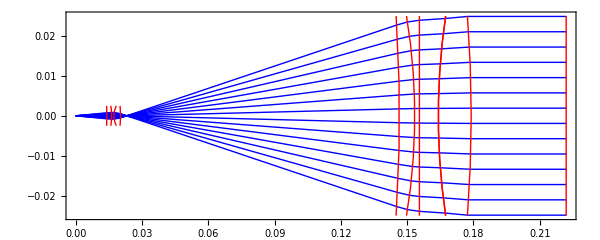

```mathematica
Block[{d0=pC230260P,
           d1=frontFocusTriplet +qC230260P,
           d2=43mm},
g={RayPathGraphics[opticsC230260PTriplet[d0,d1,d2]][initialBundle[θFiber],Blue], InterfaceGraphics[opticsC230260PTriplet[d0,d1,d2]]};
Show[g,PlotRange->{{0,All},{-30mm,30mm}},PlotRangeClipping->True,Frame->True,AspectRatio->Automatic,ImageSize->600, FrameLabel->{"Test"}]]
```

```mathematica
?Ray
```

Ray[x,y,slope,n] represents a ray where the ray starts at {x,y} with slope slope in a material of refractive index n.  The slope is the tangent of the angle to the optical axis.

```mathematica
Block[{d0=pC230260P,
           d1=frontFocusTriplet +qC230260P,
           d2=43mm},
g={RayPathGraphics[opticsC230260PTriplet[d0,d1,d2]][initialBundle[θFiber,0mm],Blue], InterfaceGraphics[opticsC230260PTriplet[d0,d1,d2]]};
Show[g,PlotRange->{{0,All},{-50mm,50mm}},PlotRangeClipping->True,Frame->True,AspectRatio->Automatic,ImageSize->600, FrameLabel->{"Test"}]]
```

-Graphics-

This selects the slope of each ray which is displaced transversely from the front focal point and takes their average.

```mathematica
{#,Median[Cases[Block[{d0=pC230260P,
           d1=frontFocusTriplet +qC230260P,
           d2=43mm},PropagateRayBundle[initialBundle[θFiber,# mm],opticsC230260PTriplet[d0,d1,d2]]],Ray[x_,y_,slope_,n_]:>{y,slope} ]]}&/@Range[0,3,0.1]
```

{{0.,Median[{}]},{0.1,Median[{}]},{0.2,Median[{}]},{0.3,Median[{}]},{0.4,Median[{}]},{0.5,Median[{}]},{0.6,Median[{}]},{0.7,Median[{}]},{0.8,Median[{}]},{0.9,Median[{}]},{1.,Median[{}]},{1.1,Median[{}]},{1.2,Median[{}]},{1.3,Median[{}]},{1.4,Median[{}]},{1.5,Median[{}]},{1.6,Median[{}]},{1.7,Median[{}]},{1.8,Median[{}]},{1.9,Median[{}]},{2.,Median[{}]},{2.1,Median[{}]},{2.2,Median[{}]},{2.3,Median[{}]},{2.4,Median[{}]},{2.5,Median[{}]},{2.6,Median[{}]},{2.7,Median[{}]},{2.8,Median[{}]},{2.9,Median[{}]},{3.,Median[{}]}}

Plotting the average slope as a function of displacement gives the following dependence. Approximately 1 mrad/mm

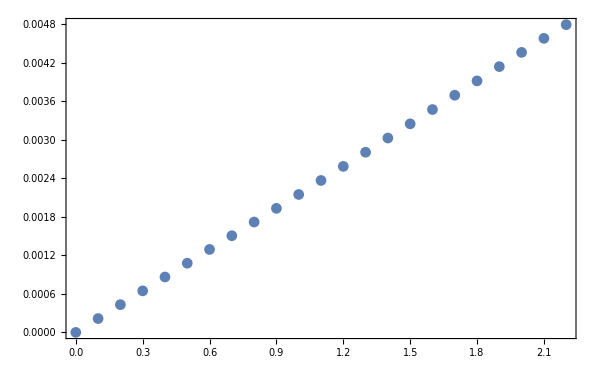

Now I’ll do the same for a horizontal displacement

```mathematica
initialBundle[θmax_,ydisp_:0,zdisp_:0]:=With[{npts=100},Table[Ray[zdisp,ydisp,θ,1],{θ,-θmax,θmax,(2θmax)/(npts-1)}]]
```

```mathematica
?initialBundle
```

Global`initialBundle

initialBundle[θmax_]:=With[{npts=30},Table[Ray[0.,0.,θ,1.],{θ,-θmax,θmax,(2 θmax)/(npts-1)}]]
 
initialBundle[θmax_,ydisp_:0,zdisp_:0]:=With[{npts=100},Table[Ray[zdisp,ydisp,θ,1],{θ,-θmax,θmax,(2 θmax)/(npts-1)}]]

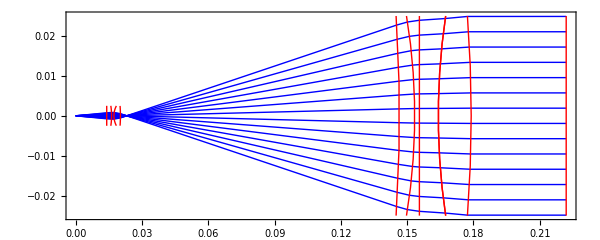
```mathematica
multiDataExport[-Graphics-,"ray_trace"]
```

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/ray_trace001.csv.

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/ray_trace002.csv.

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/ray_trace003.csv.

General::stop: Further output of OpenWrite::noopen will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
qC230260P
```

0.00285037

```mathematica
frontFocusTriplet
```

0.123458

### Wavefront quality

Look at the wavefront for the expander and triplet combination.

```mathematica
wavefrontPlotC230260PTriplet[d0_,d1_,d2_,opts___]:=
Block[{outputBundle,θ=θFiber},
             outputBundle=PropagateRayBundle[initialBundle[θ],opticsC230260PTriplet[d0,d1,d2]];
             ListLinePlot[WavefrontFromRayBundle[outputBundle]/.{y_,shift_}:>{y/mm,shift/($λ)},opts,
                                          Frame->True,FrameLabel->{"transverse position (mm)","wavefront position/λ"},GridLines->Automatic,GridLinesStyle->LightGray]]
```

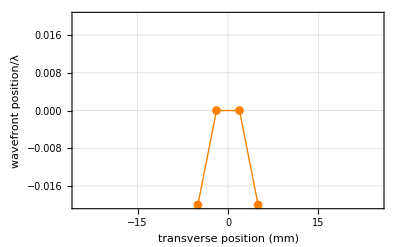

```mathematica
Magnify[C230260PTripletPlot=wavefrontPlotC230260PTriplet[pC230260P,frontFocusTriplet + qC230260P,43mm,PlotStyle->{Orange,Thick},PlotMarkers->Automatic,PlotRange->{-0.02,0.02}],3/2]
```

The wavefront is fairly insensitive to movements of the expander (with the triplet lens tracking the moving focus).  That presumably shows that the aspheric lens aberrations are well-controlled even when the source isn’t at the focus.  Here we shift the expander by 2mm and move the triplet to maintain collimation

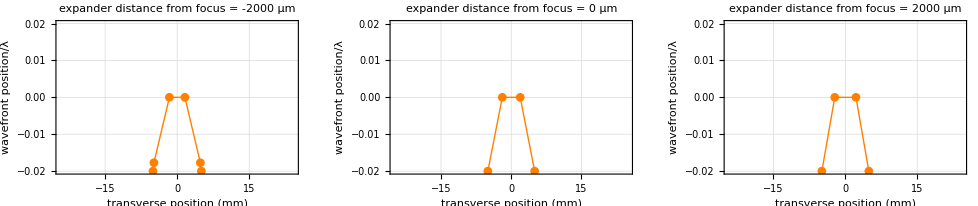

```mathematica
GraphicsRow[Table[wavefrontPlotC230260PTriplet[pC230260P + d µm,frontFocusTriplet + q/.p->(pC230260P+d µm),43mm,PlotStyle->{Orange,Thick},PlotMarkers->Automatic,PlotRange->{-0.02,0.02},ImageSize->300,PlotLabel->"expander distance from focus = "<>ToString[d]<>" µm"],{d,-2000,2000,2000}]]
```

If the triplet stays fixed at the ideal position then the sensitivity to expander position is much larger.  This is 100x smaller shift than above.

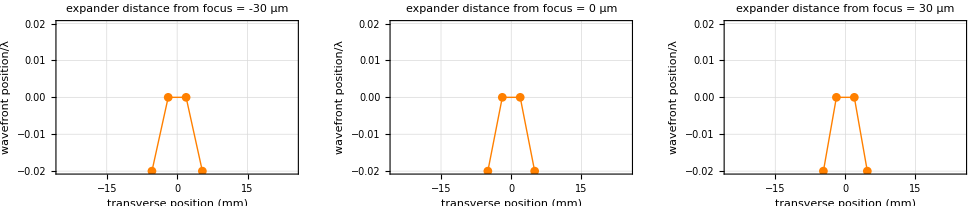

```mathematica
GraphicsRow[Table[wavefrontPlotC230260PTriplet[pC230260P + d µm,frontFocusTriplet + qC230260P,43mm,PlotStyle->{Orange,Thick},PlotMarkers->Automatic,PlotRange->{-0.02,0.02},ImageSize->300,PlotLabel->"expander distance from focus = "<>ToString[d]<>" µm"],{d,-30,30,30}]]
```

The sensitivity of the wavefront flatness to the position of the triplet lens is the same as with the lens alone.  And the position determined by geometrical optics is the optimum one.

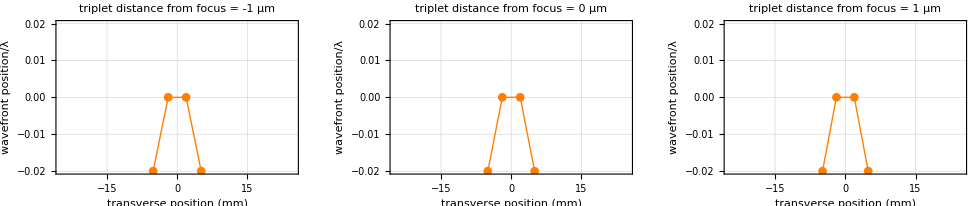

```mathematica
GraphicsRow[Table[wavefrontPlotC230260PTriplet[pC230260P,d µm + frontFocusTriplet + qC230260P,43mm,PlotStyle->{Orange,Thick},PlotMarkers->Automatic,PlotRange->{-0.02,0.02},ImageSize->300,PlotLabel->"triplet distance from focus = "<>ToString[d]<>" µm"],{d,-1,1,1}]]
```

### Interferometer phase error

A repeat of the section above.

```mathematica
phaseErrorPlotC230260PTriplet[d0_,d1_,opts___]:=
Block[{outputBundle1, outputBundle2,θ=θFiber,direct=43mm,retro=129mm,front1,front2},
             outputBundle1=PropagateRayBundle[initialBundle[θ],opticsC230260PTriplet[d0,d1,direct]];
             outputBundle2=PropagateRayBundle[initialBundle[θ],opticsC230260PTriplet[d0,d1,retro]];
             front1=WavefrontFromRayBundle[outputBundle1]/.{y_,shift_}:>{y/mm,shift/($λ)};
             front2=WavefrontFromRayBundle[outputBundle2]/.{y_,shift_}:>{y/mm,shift/($λ-Δλ)};
GraphicsRow[{ListLinePlot[{front1, front2},opts,Frame->True,FrameLabel->{"transverse position (mm)","wavefront position/λ"},GridLines->Automatic,GridLinesStyle->LightGray,PlotRange->All,PlotStyle->Thick],
ListLinePlot[Transpose[{front1⟦All,1⟧,front1⟦All,2⟧-front2⟦All,2⟧}],opts,Frame->True,FrameLabel->{"transverse position (mm)","differential shift/λ"},GridLines->Automatic,GridLinesStyle->LightGray,PlotRange->{-0.02,0.02},PlotStyle->Thick]},ImageSize->800]]
```

```mathematica
?opticsC230260PTriplet
```

Global`opticsC230260PTriplet

opticsC230260PTriplet[d0_,d1_,d2_]:=Flatten[{Aspheric[{R1,k1,A4,A6,A8,A10,A12,A14,A16},{R2,k2,B4,B6,B8,B10,B12,B14,B16},TC1,N1,Dia][d0]/.lens4,Aspheric[{R1,k1,A4,A6,A8,A10,A12,A14,A16},{R2,k2,B4,B6,B8,B10,B12,B14,B16},TC1,N1,Dia][d0+(TC1/.lens4)+1.067 mm]/.lens5,AirSpacedTriplet[R1,R2,R3,R4,R5,R6,TC1,TC2,TC3,gap1,gap2,N1,N2,N3,Dia][d0+(TC1/.lens4)+1.067 mm+(TC1/.lens5)+d1]/.lens3,Interface[∞,d0+(TC1/.lens4)+1.067 mm+(TC1/.lens5)+d1+(TC1+TC2+TC3+gap1+gap2/.lens3)+d2,1,25 mm]}]

```mathematica
phaseErrorPlotC230260PTriplet2[d0_,d1_,ydisp_:0,opts___]:=Block[{outputBundle1,outputBundle2,θ=θFiber,direct=50 mm,retro=150 mm,front1,front2},outputBundle1=PropagateRayBundle[initialBundle[θ,ydisp],opticsC230260PTriplet[d0,d1,direct]];outputBundle2=PropagateRayBundle[initialBundle[θ,ydisp],opticsC230260PTriplet[d0,d1,retro]];
front1=WavefrontFromRayBundle[outputBundle1]/.{y_,shift_}:>{y/mm,shift/($λ)};front2=WavefrontFromRayBundle[outputBundle2]/.{y_,shift_}:>{y/mm,shift/($λ-Δλ)};ListLinePlot[Transpose[{front1⟦All,1⟧,front1⟦All,2⟧-front2⟦All,2⟧}],opts,Frame->True,FrameLabel->{"transverse position (mm)","differential shift/λ"},GridLines->Automatic,GridLinesStyle->LightGray,PlotRange->{-0.05,0.05},PlotStyle->Thick]
]
```

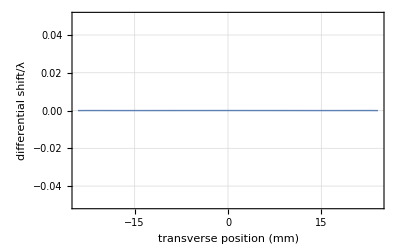
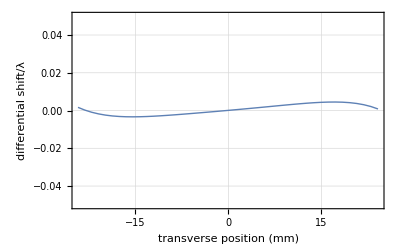
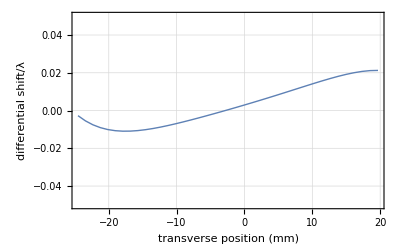
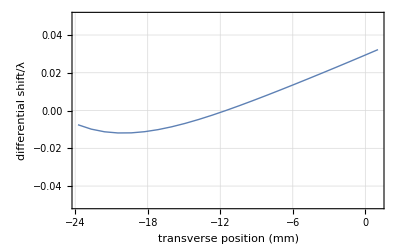

```mathematica
ydips = phaseErrorPlotC230260PTriplet2[pC230260P,0µm +frontFocusTriplet + qC230260P,# mm]&/@{0,0.5,1,1.5}
```

```mathematica
dataExport[#,"transverse_disp_"<>IntegerString[#2,10,3]]&~MapIndexed~ydips
```

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/transverse_disp_001.csv.

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/transverse_disp_002.csv.

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/transverse_disp_003.csv.

General::stop: Further output of OpenWrite::noopen will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed}

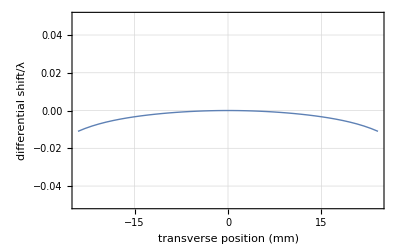
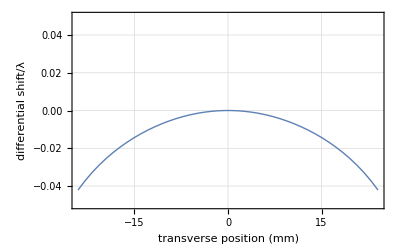
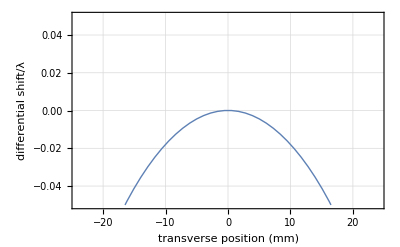
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
zdisp = phaseErrorPlotC230260PTriplet2[pC230260P,-# µm +frontFocusTriplet + qC230260P]&/@{0,300,600,1000}
```

```mathematica
dataExport[#,"longitudinal_disp_"<>IntegerString[#2,10,3]]&~MapIndexed~zdisp
```

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/longitudinal_disp_001.csv.

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/longitudinal_disp_002.csv.

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/longitudinal_disp_003.csv.

General::stop: Further output of OpenWrite::noopen will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed}

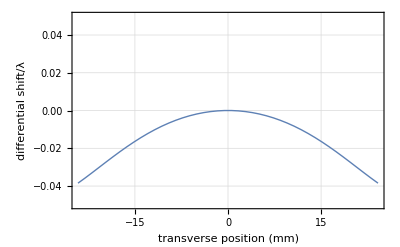

```mathematica
phaseErrorPlotC230260PTriplet2[pC230260P,600µm +frontFocusTriplet + qC230260P]
```

The triplet can be defocused by ±600µm before the phase error is equivalent to λ/100 at 12mm.

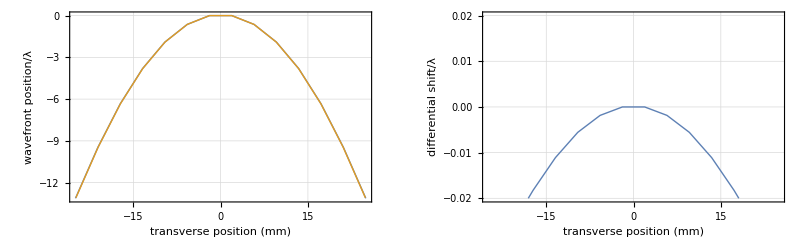

```mathematica
phaseErrorPlotC230260PTriplet[pC230260P,600µm +frontFocusTriplet + qC230260P]
```

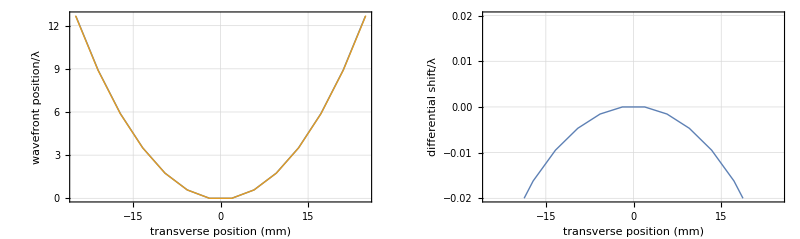

```mathematica
phaseErrorPlotC230260PTriplet[pC230260P,-600µm +frontFocusTriplet + qC230260P]
```

### Gaussian beam treatment

The triplet will transform the waist at the end of the fiber to a waist at the focus on the other side, which is close to the field seen by the atoms from the retroreflection.  The wavefront 43mm from the lens will be curved, so perhaps that will make a bigger phase difference.  So here we consider the transformation of the waist at the fiber by the triplet.

This is the complex beam parameter of the waist at the end of the fiber, which we take to be at the origin

```mathematica
q0=qWaist[ω0, 0, λ];
```

This describes the optical system.  It is adequate here to treat the three lenses as thin.

```mathematica
train:=Train[Translation[d0],Lens[f1,f1],Translation[1.067mm],Lens[f2,f2],Translation[d1,1],Lens[f,f]];
```

This is the complex beam parameter after the triplet lens

```mathematica
qLens=Transform[train][q0]//Simplify;
```

Spot size at the lens is now 44 mm

```mathematica
SpotSize[qLens,λ]/.{f1->15.37mm, f2->4.53mm,f->127mm, d0->15.37mm,d1->127mm+2.9mm,ω0->2.4µm, λ->780nm}
```

0.0440052

### Important dimensions

The distance from the fiber tip to the f = 15.3 mm lens surface on-axis is 13.99 mm.
The beam is then brought to a focus 2.850 mm from the back surface of the f = 4.5 mm lens.
The distance between the surfaces of the f = 4.5 mm asphere and the triplet is therefore 2.850 mm + 123.434 mm = 126.284 mm

### Ray Tracing Sim

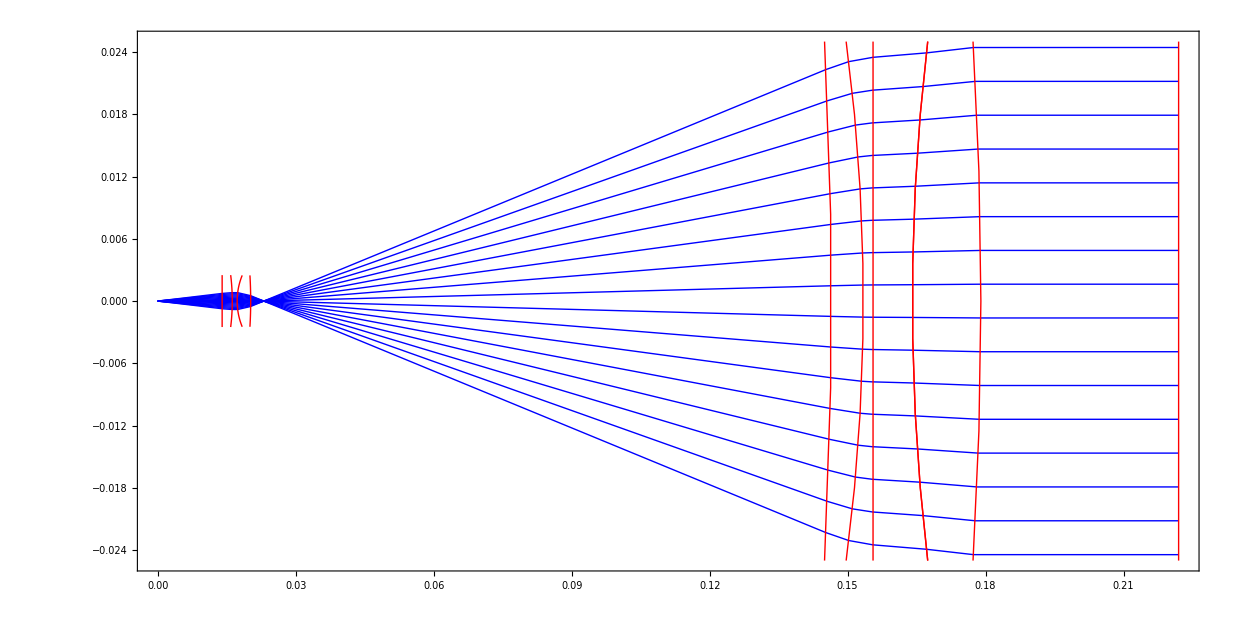

-Graphics-

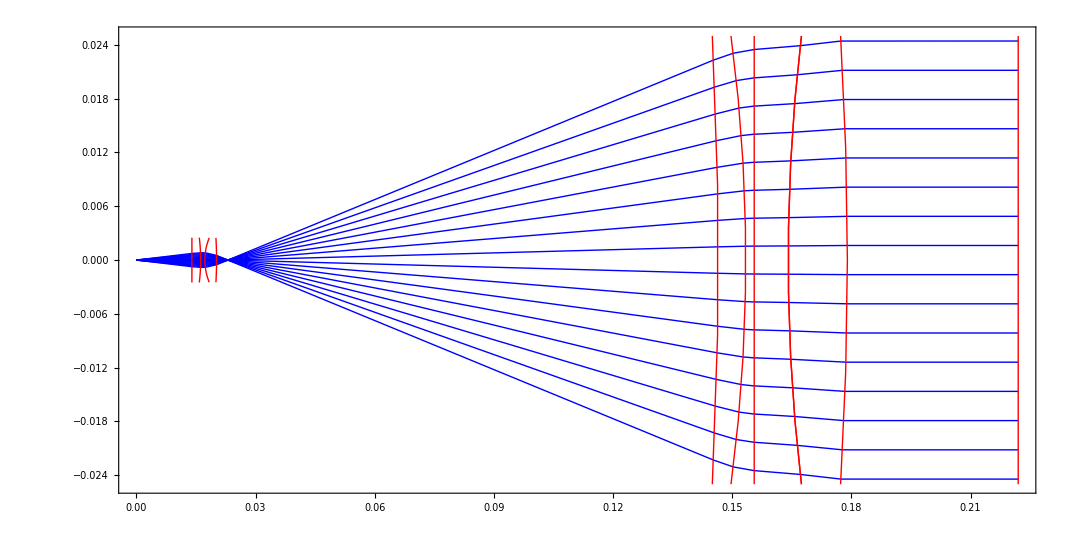
```mathematica
data=Cases[First@-Graphics-,Circle[{x_,y_},r_,{tm_,tmax_}]:>Table[{r Cos[θ]+x,r Sin[θ]+y},{θ,Subdivide[tm,tmax,100]}],-1];
```

```mathematica
?Circle
```

Circle[{x,y},r] represents a circle of radius r centered at {x,y}.
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},{r_x,r_y}] gives an axis-aligned ellipse with semiaxes lengths r_x and r_y.
Circle[{x,y},…,{θ_1,θ_2}] gives a circular or ellipse arc from angle θ_1 to θ_2.

```mathematica
?Subdivide
```

Subdivide[n] generates the list {0,1/n,2/n,…,1}.
Subdivide[x_max,n] generates the list of values obtained by subdividing the interval 0 to x_max into n equal parts.
Subdivide[x_min,x_max,n] generates the list of values from subdividing the interval x_min to x_max.

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
data//Dimensions
```

{6,101,2}

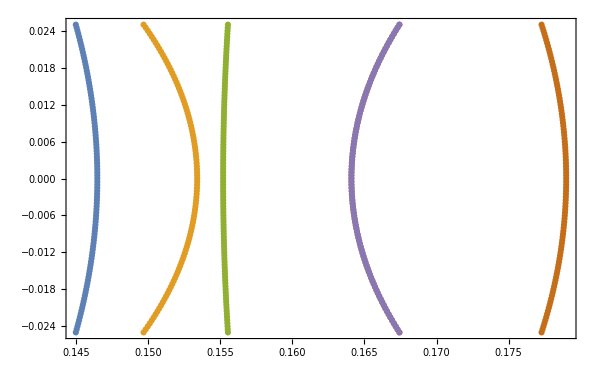

```mathematica
ListPlot[data]
```

```mathematica
Export["PlotData/ray_trace"<>IntegerString[#2+19,10,3]<>".csv",#,"CSV"]&~MapIndexed~data
```

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/ray_trace020.csv.

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/ray_trace021.csv.

Export::nodir: Directory /home/jimmy/PlotData/ does not exist.

General::stop: Further output of Export::nodir will be suppressed during this calculation.

OpenWrite::noopen: Cannot open /home/jimmy/PlotData/ray_trace022.csv.

General::stop: Further output of OpenWrite::noopen will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
multiDataExport[%102,"ray_lenses"]
```

First::normal: Nonatomic expression expected at position 1 in First[Null].

{}

```mathematica
FullForm[%102]
```

Null

```mathematica
data
```

{{{0.14499,-0.025},{0.145049,-0.0245023},{0.145107,-0.0240045},{0.145164,-0.0235065},{0.145219,-0.0230084},{0.145273,-0.0225101},{0.145326,-0.0220118},{0.145378,-0.0215133},{0.145429,-0.0210147},{0.145478,-0.0205159},{0.145527,-0.0200171},{0.145574,-0.0195181},{0.14562,-0.019019},{0.145664,-0.0185198},{0.145708,-0.0180205},{0.14575,-0.0175212},{0.145792,-0.0170217},{0.145831,-0.0165221},{0.14587,-0.0160224},{0.145908,-0.0155226},{0.145944,-0.0150228},{0.145979,-0.0145228},{0.146014,-0.0140228},{0.146046,-0.0135227},{0.146078,-0.0130225},{0.146108,-0.0125222},{0.146138,-0.0120219},{0.146166,-0.0115215},{0.146193,-0.011021},{0.146218,-0.0105205},{0.146243,-0.0100199},{0.146266,-0.00951927},{0.146288,-0.00901857},{0.146309,-0.00851782},{0.146329,-0.00801703},{0.146347,-0.00751618},{0.146365,-0.0070153},{0.146381,-0.00651437},{0.146396,-0.00601341},{0.146409,-0.00551241},{0.146422,-0.00501138},{0.146433,-0.00451032},{0.146443,-0.00400924},{0.146452,-0.00350814},{0.14646,-0.00300701},{0.146467,-0.00250587},{0.146472,-0.00200471},{0.146476,-0.00150354},{0.146479,-0.00100237},{0.146481,-0.000501185},{0.146482,0.},{0.146481,0.000501185},{0.146479,0.00100237},{0.146476,0.00150354},{0.146472,0.00200471},{0.146467,0.00250587},{0.14646,0.00300701},{0.146452,0.00350814},{0.146443,0.00400924},{0.146433,0.00451032},{0.146422,0.00501138},{0.146409,0.00551241},{0.146396,0.00601341},{0.146381,0.00651437},{0.146365,0.0070153},{0.146347,0.00751618},{0.146329,0.00801703},{0.146309,0.00851782},{0.146288,0.00901857},{0.146266,0.00951927},{0.146243,0.0100199},{0.146218,0.0105205},{0.146193,0.011021},{0.146166,0.0115215},{0.146138,0.0120219},{0.146108,0.0125222},{0.146078,0.0130225},{0.146046,0.0135227},{0.146014,0.0140228},{0.145979,0.0145228},{0.145944,0.0150228},{0.145908,0.0155226},{0.14587,0.0160224},{0.145831,0.0165221},{0.145792,0.0170217},{0.14575,0.0175212},{0.145708,0.0180205},{0.145664,0.0185198},{0.14562,0.019019},{0.145574,0.0195181},{0.145527,0.0200171},{0.145478,0.0205159},{0.145429,0.0210147},{0.145378,0.0215133},{0.145326,0.0220118},{0.145273,0.0225101},{0.145219,0.0230084},{0.145164,0.0235065},{0.145107,0.0240045},{0.145049,0.0245023},{0.14499,0.025}},{{0.149688,-0.025},{0.149834,-0.0245142},{0.149977,-0.0240275},{0.150117,-0.02354},{0.150255,-0.0230516},{0.15039,-0.0225625},{0.150521,-0.0220725},{0.15065,-0.0215818},{0.150776,-0.0210904},{0.150899,-0.0205982},{0.151019,-0.0201053},{0.151136,-0.0196117},{0.151251,-0.0191174},{0.151362,-0.0186224},{0.151471,-0.0181268},{0.151576,-0.0176306},{0.151679,-0.0171338},{0.151778,-0.0166363},{0.151875,-0.0161383},{0.151969,-0.0156397},{0.15206,-0.0151406},{0.152148,-0.0146409},{0.152232,-0.0141407},{0.152314,-0.0136401},{0.152393,-0.0131389},{0.15247,-0.0126373},{0.152543,-0.0121353},{0.152613,-0.0116328},{0.15268,-0.01113},{0.152744,-0.0106267},{0.152805,-0.0101231},{0.152864,-0.00961912},{0.152919,-0.00911481},{0.152971,-0.00861018},{0.153021,-0.00810525},{0.153067,-0.00760004},{0.15311,-0.00709457},{0.153151,-0.00658885},{0.153188,-0.0060829},{0.153223,-0.00557673},{0.153254,-0.00507038},{0.153282,-0.00456384},{0.153308,-0.00405715},{0.15333,-0.00355031},{0.15335,-0.00304336},{0.153366,-0.00253629},{0.15338,-0.00202914},{0.15339,-0.00152192},{0.153398,-0.00101464},{0.153402,-0.000507329},{0.153404,0.},{0.153402,0.000507329},{0.153398,0.00101464},{0.15339,0.00152192},{0.15338,0.00202914},{0.153366,0.00253629},{0.15335,0.00304336},{0.15333,0.00355031},{0.153308,0.00405715},{0.153282,0.00456384},{0.153254,0.00507038},{0.153223,0.00557673},{0.153188,0.0060829},{0.153151,0.00658885},{0.15311,0.00709457},{0.153067,0.00760004},{0.153021,0.00810525},{0.152971,0.00861018},{0.152919,0.00911481},{0.152864,0.00961912},{0.152805,0.0101231},{0.152744,0.0106267},{0.15268,0.01113},{0.152613,0.0116328},{0.152543,0.0121353},{0.15247,0.0126373},{0.152393,0.0131389},{0.152314,0.0136401},{0.152232,0.0141407},{0.152148,0.0146409},{0.15206,0.0151406},{0.151969,0.0156397},{0.151875,0.0161383},{0.151778,0.0166363},{0.151679,0.0171338},{0.151576,0.0176306},{0.151471,0.0181268},{0.151362,0.0186224},{0.151251,0.0191174},{0.151136,0.0196117},{0.151019,0.0201053},{0.150899,0.0205982},{0.150776,0.0210904},{0.15065,0.0215818},{0.150521,0.0220725},{0.15039,0.0225625},{0.150255,0.0230516},{0.150117,0.02354},{0.149977,0.0240275},{0.149834,0.0245142},{0.149688,0.025}},{{0.155535,0.025},{0.155522,0.0245001},{0.155509,0.0240002},{0.155497,0.0235003},{0.155484,0.0230004},{0.155472,0.0225005},{0.15546,0.0220006},{0.155449,0.0215007},{0.155438,0.0210007},{0.155427,0.0205008},{0.155416,0.0200008},{0.155405,0.0195009},{0.155395,0.0190009},{0.155385,0.018501},{0.155375,0.018001},{0.155366,0.017501},{0.155357,0.0170011},{0.155348,0.0165011},{0.155339,0.0160011},{0.155331,0.0155011},{0.155323,0.0150011},{0.155315,0.0145011},{0.155307,0.0140011},{0.1553,0.0135011},{0.155293,0.0130011},{0.155286,0.0125011},{0.15528,0.0120011},{0.155274,0.0115011},{0.155268,0.011001},{0.155262,0.010501},{0.155256,0.010001},{0.155251,0.00950096},{0.155246,0.00900092},{0.155242,0.00850088},{0.155237,0.00800084},{0.155233,0.0075008},{0.155229,0.00700076},{0.155226,0.00650071},{0.155222,0.00600067},{0.155219,0.00550062},{0.155217,0.00500056},{0.155214,0.00450051},{0.155212,0.00400046},{0.15521,0.0035004},{0.155208,0.00300035},{0.155207,0.00250029},{0.155205,0.00200023},{0.155204,0.00150018},{0.155204,0.00100012},{0.155203,0.000500059},{0.155203,1.1527×10^-16},{0.155203,-0.000500059},{0.155204,-0.00100012},{0.155204,-0.00150018},{0.155205,-0.00200023},{0.155207,-0.00250029},{0.155208,-0.00300035},{0.15521,-0.0035004},{0.155212,-0.00400046},{0.155214,-0.00450051},{0.155217,-0.00500056},{0.155219,-0.00550062},{0.155222,-0.00600067},{0.155226,-0.00650071},{0.155229,-0.00700076},{0.155233,-0.0075008},{0.155237,-0.00800084},{0.155242,-0.00850088},{0.155246,-0.00900092},{0.155251,-0.00950096},{0.155256,-0.010001},{0.155262,-0.010501},{0.155268,-0.011001},{0.155274,-0.0115011},{0.15528,-0.0120011},{0.155286,-0.0125011},{0.155293,-0.0130011},{0.1553,-0.0135011},{0.155307,-0.0140011},{0.155315,-0.0145011},{0.155323,-0.0150011},{0.155331,-0.0155011},{0.155339,-0.0160011},{0.155348,-0.0165011},{0.155357,-0.0170011},{0.155366,-0.017501},{0.155375,-0.018001},{0.155385,-0.018501},{0.155395,-0.0190009},{0.155405,-0.0195009},{0.155416,-0.0200008},{0.155427,-0.0205008},{0.155438,-0.0210007},{0.155449,-0.0215007},{0.15546,-0.0220006},{0.155472,-0.0225005},{0.155484,-0.0230004},{0.155497,-0.0235003},{0.155509,-0.0240002},{0.155522,-0.0245001},{0.155535,-0.025}},{{0.167424,0.025},{0.167293,0.0245114},{0.167164,0.0240221},{0.167038,0.0235321},{0.166915,0.0230415},{0.166794,0.0225502},{0.166676,0.0220583},{0.166561,0.0215658},{0.166448,0.0210726},{0.166338,0.0205789},{0.16623,0.0200846},{0.166125,0.0195897},{0.166023,0.0190943},{0.165923,0.0185984},{0.165826,0.0181019},{0.165731,0.0176049},{0.165639,0.0171074},{0.16555,0.0166095},{0.165463,0.0161111},{0.165379,0.0156122},{0.165298,0.0151129},{0.165219,0.0146132},{0.165143,0.014113},{0.16507,0.0136125},{0.164999,0.0131116},{0.164931,0.0126103},{0.164866,0.0121087},{0.164803,0.0116067},{0.164743,0.0111044},{0.164685,0.0106018},{0.16463,0.0100989},{0.164578,0.00959567},{0.164529,0.00909221},{0.164482,0.00858849},{0.164438,0.00808453},{0.164396,0.00758035},{0.164358,0.00707595},{0.164322,0.00657135},{0.164288,0.00606657},{0.164257,0.00556162},{0.164229,0.00505652},{0.164204,0.00455127},{0.164181,0.00404589},{0.164161,0.00354041},{0.164143,0.00303482},{0.164129,0.00252914},{0.164117,0.0020234},{0.164107,0.0015176},{0.164101,0.00101176},{0.164097,0.000505886},{0.164095,1.17015×10^-17},{0.164097,-0.000505886},{0.164101,-0.00101176},{0.164107,-0.0015176},{0.164117,-0.0020234},{0.164129,-0.00252914},{0.164143,-0.00303482},{0.164161,-0.00354041},{0.164181,-0.00404589},{0.164204,-0.00455127},{0.164229,-0.00505652},{0.164257,-0.00556162},{0.164288,-0.00606657},{0.164322,-0.00657135},{0.164358,-0.00707595},{0.164396,-0.00758035},{0.164438,-0.00808453},{0.164482,-0.00858849},{0.164529,-0.00909221},{0.164578,-0.00959567},{0.16463,-0.0100989},{0.164685,-0.0106018},{0.164743,-0.0111044},{0.164803,-0.0116067},{0.164866,-0.0121087},{0.164931,-0.0126103},{0.164999,-0.0131116},{0.16507,-0.0136125},{0.165143,-0.014113},{0.165219,-0.0146132},{0.165298,-0.0151129},{0.165379,-0.0156122},{0.165463,-0.0161111},{0.16555,-0.0166095},{0.165639,-0.0171074},{0.165731,-0.0176049},{0.165826,-0.0181019},{0.165923,-0.0185984},{0.166023,-0.0190943},{0.166125,-0.0195897},{0.16623,-0.0200846},{0.166338,-0.0205789},{0.166448,-0.0210726},{0.166561,-0.0215658},{0.166676,-0.0220583},{0.166794,-0.0225502},{0.166915,-0.0230415},{0.167038,-0.0235321},{0.167164,-0.0240221},{0.167293,-0.0245114},{0.167424,-0.025}},{{0.167424,0.025},{0.167293,0.0245114},{0.167164,0.0240221},{0.167038,0.0235321},{0.166915,0.0230415},{0.166794,0.0225502},{0.166676,0.0220583},{0.166561,0.0215658},{0.166448,0.0210726},{0.166338,0.0205789},{0.16623,0.0200846},{0.166125,0.0195897},{0.166023,0.0190943},{0.165923,0.0185984},{0.165826,0.0181019},{0.165731,0.0176049},{0.165639,0.0171074},{0.16555,0.0166095},{0.165463,0.0161111},{0.165379,0.0156122},{0.165298,0.0151129},{0.165219,0.0146132},{0.165143,0.014113},{0.16507,0.0136125},{0.164999,0.0131116},{0.164931,0.0126103},{0.164866,0.0121087},{0.164803,0.0116067},{0.164743,0.0111044},{0.164685,0.0106018},{0.16463,0.0100989},{0.164578,0.00959567},{0.164529,0.00909221},{0.164482,0.00858849},{0.164438,0.00808453},{0.164396,0.00758035},{0.164358,0.00707595},{0.164322,0.00657135},{0.164288,0.00606657},{0.164257,0.00556162},{0.164229,0.00505652},{0.164204,0.00455127},{0.164181,0.00404589},{0.164161,0.00354041},{0.164143,0.00303482},{0.164129,0.00252914},{0.164117,0.0020234},{0.164107,0.0015176},{0.164101,0.00101176},{0.164097,0.000505886},{0.164095,1.17015×10^-17},{0.164097,-0.000505886},{0.164101,-0.00101176},{0.164107,-0.0015176},{0.164117,-0.0020234},{0.164129,-0.00252914},{0.164143,-0.00303482},{0.164161,-0.00354041},{0.164181,-0.00404589},{0.164204,-0.00455127},{0.164229,-0.00505652},{0.164257,-0.00556162},{0.164288,-0.00606657},{0.164322,-0.00657135},{0.164358,-0.00707595},{0.164396,-0.00758035},{0.164438,-0.00808453},{0.164482,-0.00858849},{0.164529,-0.00909221},{0.164578,-0.00959567},{0.16463,-0.0100989},{0.164685,-0.0106018},{0.164743,-0.0111044},{0.164803,-0.0116067},{0.164866,-0.0121087},{0.164931,-0.0126103},{0.164999,-0.0131116},{0.16507,-0.0136125},{0.165143,-0.014113},{0.165219,-0.0146132},{0.165298,-0.0151129},{0.165379,-0.0156122},{0.165463,-0.0161111},{0.16555,-0.0166095},{0.165639,-0.0171074},{0.165731,-0.0176049},{0.165826,-0.0181019},{0.165923,-0.0185984},{0.166023,-0.0190943},{0.166125,-0.0195897},{0.16623,-0.0200846},{0.166338,-0.0205789},{0.166448,-0.0210726},{0.166561,-0.0215658},{0.166676,-0.0220583},{0.166794,-0.0225502},{0.166915,-0.0230415},{0.167038,-0.0235321},{0.167164,-0.0240221},{0.167293,-0.0245114},{0.167424,-0.025}},{{0.177279,-0.025},{0.177346,-0.024503},{0.177412,-0.0240058},{0.177477,-0.0235085},{0.177541,-0.023011},{0.177603,-0.0225133},{0.177663,-0.0220154},{0.177723,-0.0215174},{0.177781,-0.0210192},{0.177837,-0.0205209},{0.177893,-0.0200224},{0.177947,-0.0195237},{0.177999,-0.0190249},{0.178051,-0.018526},{0.1781,-0.0180269},{0.178149,-0.0175277},{0.178196,-0.0170284},{0.178242,-0.0165289},{0.178286,-0.0160293},{0.178329,-0.0155296},{0.178371,-0.0150298},{0.178411,-0.0145299},{0.17845,-0.0140299},{0.178488,-0.0135297},{0.178524,-0.0130295},{0.178559,-0.0125291},{0.178592,-0.0120287},{0.178624,-0.0115282},{0.178655,-0.0110276},{0.178685,-0.0105269},{0.178713,-0.0100261},{0.178739,-0.00952526},{0.178765,-0.00902434},{0.178789,-0.00852336},{0.178811,-0.00802231},{0.178832,-0.00752121},{0.178852,-0.00702005},{0.178871,-0.00651883},{0.178888,-0.00601757},{0.178903,-0.00551626},{0.178918,-0.00501492},{0.178931,-0.00451353},{0.178942,-0.00401211},{0.178953,-0.00351066},{0.178962,-0.00300919},{0.178969,-0.00250769},{0.178975,-0.00200618},{0.17898,-0.00150464},{0.178984,-0.0010031},{0.178986,-0.000501553},{0.178986,0.},{0.178986,0.000501553},{0.178984,0.0010031},{0.17898,0.00150464},{0.178975,0.00200618},{0.178969,0.00250769},{0.178962,0.00300919},{0.178953,0.00351066},{0.178942,0.00401211},{0.178931,0.00451353},{0.178918,0.00501492},{0.178903,0.00551626},{0.178888,0.00601757},{0.178871,0.00651883},{0.178852,0.00702005},{0.178832,0.00752121},{0.178811,0.00802231},{0.178789,0.00852336},{0.178765,0.00902434},{0.178739,0.00952526},{0.178713,0.0100261},{0.178685,0.0105269},{0.178655,0.0110276},{0.178624,0.0115282},{0.178592,0.0120287},{0.178559,0.0125291},{0.178524,0.0130295},{0.178488,0.0135297},{0.17845,0.0140299},{0.178411,0.0145299},{0.178371,0.0150298},{0.178329,0.0155296},{0.178286,0.0160293},{0.178242,0.0165289},{0.178196,0.0170284},{0.178149,0.0175277},{0.1781,0.0180269},{0.178051,0.018526},{0.177999,0.0190249},{0.177947,0.0195237},{0.177893,0.0200224},{0.177837,0.0205209},{0.177781,0.0210192},{0.177723,0.0215174},{0.177663,0.0220154},{0.177603,0.0225133},{0.177541,0.023011},{0.177477,0.0235085},{0.177412,0.0240058},{0.177346,0.024503},{0.177279,0.025}}}

```mathematica
First@-Graphics-
```

{{RGBColor[0, 0, 1],Line[{{0.,0.},{0.0139905,-0.000738841},{0.0161546,-0.000810446},{0.0173693,-0.000810446},{0.0201903,-0.000521044},{0.145295,0.0223069},{0.15025,0.0230679},{0.155496,0.0234829},{0.167135,0.0239098},{0.167135,0.0239098},{0.177356,0.0244278},{0.221986,0.0244303}}],Line[{{0.,0.},{0.0139905,-0.000640329},{0.0161635,-0.000702656},{0.0173414,-0.000702656},{0.0201921,-0.000449383},{0.145594,0.0192951},{0.15104,0.0200171},{0.155423,0.0203177},{0.166357,0.0206659},{0.166357,0.0206659},{0.177764,0.0211657},{0.221986,0.0211668}}],Line[{{0.,0.},{0.0139905,-0.000541817},{0.0161712,-0.000594751},{0.0173175,-0.000594751},{0.0201937,-0.000378675},{0.145849,0.0162992},{0.151715,0.0169552},{0.15536,0.0171667},{0.165701,0.0174458},{0.165701,0.0174458},{0.178112,0.0179051},{0.221986,0.0179055}}],Line[{{0.,0.},{0.0139905,-0.000443305},{0.0161776,-0.000486748},{0.0172977,-0.000486748},{0.020195,-0.000308761},{0.146059,0.0133169},{0.152275,0.0138841},{0.155308,0.0140281},{0.165163,0.014246},{0.165163,0.014246},{0.178402,0.0146462},{0.221986,0.0146463}}],Line[{{0.,0.},{0.0139905,-0.000344792},{0.0161827,-0.000378665},{0.0172818,-0.000378665},{0.020196,-0.000239491},{0.146227,0.0103459},{0.152722,0.0108058},{0.155266,0.0108998},{0.164738,0.0110628},{0.164738,0.0110628},{0.178633,0.0113891},{0.221986,0.0113892}}],Line[{{0.,0.},{0.0139905,-0.00024628},{0.0161865,-0.000270519},{0.0172699,-0.000270519},{0.0201968,-0.000170715},{0.146352,0.00738359},{0.153056,0.00772219},{0.155235,0.00777969},{0.164422,0.00789269},{0.164422,0.00789269},{0.178806,0.00813376},{0.221986,0.00813376}}],Line[{{0.,0.},{0.0139905,-0.000147768},{0.0161891,-0.00016233},{0.017262,-0.00016233},{0.0201973,-0.000102289},{0.146435,0.00442762},{0.153279,0.00463479},{0.155215,0.00466544},{0.164213,0.00473187},{0.164213,0.00473187},{0.178922,0.00487969},{0.221986,0.00487969}}],Line[{{0.,0.},{0.0139905,-0.0000492561},{0.0161904,-0.0000541128},{0.017258,-0.0000541128},{0.0201975,-0.0000340733},{0.146476,0.00147545},{0.15339,0.00154517},{0.155205,0.00155475},{0.164108,0.00157667},{0.164108,0.00157667},{0.178979,0.00162647},{0.221986,0.00162647}}],Line[{{0.,0.},{0.0139905,0.0000492561},{0.0161904,0.0000541128},{0.017258,0.0000541128},{0.0201975,0.0000340733},{0.146476,-0.00147545},{0.15339,-0.00154517},{0.155205,-0.00155475},{0.164108,-0.00157667},{0.164108,-0.00157667},{0.178979,-0.00162647},{0.221986,-0.00162647}}],Line[{{0.,0.},{0.0139905,0.000147768},{0.0161891,0.00016233},{0.017262,0.00016233},{0.0201973,0.000102289},{0.146435,-0.00442762},{0.153279,-0.00463479},{0.155215,-0.00466544},{0.164213,-0.00473187},{0.164213,-0.00473187},{0.178922,-0.00487969},{0.221986,-0.00487969}}],Line[{{0.,0.},{0.0139905,0.00024628},{0.0161865,0.000270519},{0.0172699,0.000270519},{0.0201968,0.000170715},{0.146352,-0.00738359},{0.153056,-0.00772219},{0.155235,-0.00777969},{0.164422,-0.00789269},{0.164422,-0.00789269},{0.178806,-0.00813376},{0.221986,-0.00813376}}],Line[{{0.,0.},{0.0139905,0.000344792},{0.0161827,0.000378665},{0.0172818,0.000378665},{0.020196,0.000239491},{0.146227,-0.0103459},{0.152722,-0.0108058},{0.155266,-0.0108998},{0.164738,-0.0110628},{0.164738,-0.0110628},{0.178633,-0.0113891},{0.221986,-0.0113892}}],Line[{{0.,0.},{0.0139905,0.000443305},{0.0161776,0.000486748},{0.0172977,0.000486748},{0.020195,0.000308761},{0.146059,-0.0133169},{0.152275,-0.0138841},{0.155308,-0.0140281},{0.165163,-0.014246},{0.165163,-0.014246},{0.178402,-0.0146462},{0.221986,-0.0146463}}],Line[{{0.,0.},{0.0139905,0.000541817},{0.0161712,0.000594751},{0.0173175,0.000594751},{0.0201937,0.000378675},{0.145849,-0.0162992},{0.151715,-0.0169552},{0.15536,-0.0171667},{0.165701,-0.0174458},{0.165701,-0.0174458},{0.178112,-0.0179051},{0.221986,-0.0179055}}],Line[{{0.,0.},{0.0139905,0.000640329},{0.0161635,0.000702656},{0.0173414,0.000702656},{0.0201921,0.000449383},{0.145594,-0.0192951},{0.15104,-0.0200171},{0.155423,-0.0203177},{0.166357,-0.0206659},{0.166357,-0.0206659},{0.177764,-0.0211657},{0.221986,-0.0211668}}],Line[{{0.,0.},{0.0139905,0.000738841},{0.0161546,0.000810446},{0.0173693,0.000810446},{0.0201903,0.000521044},{0.145295,-0.0223069},{0.15025,-0.0230679},{0.155496,-0.0234829},{0.167135,-0.0239098},{0.167135,-0.0239098},{0.177356,-0.0244278},{0.221986,-0.0244303}}]},{RGBColor[1, 0, 0],Line[{{0.0139905,-0.0025},{0.0139905,0.0025}}],Line[{{0.015846,-0.0025},{0.0158732,-0.0024},{0.0158992,-0.0023},{0.0159242,-0.0022},{0.015948,-0.0021},{0.0159706,-0.002},{0.0159922,-0.0019},{0.0160126,-0.0018},{0.0160319,-0.0017},{0.0160501,-0.0016},{0.0160671,-0.0015},{0.0160831,-0.0014},{0.0160979,-0.0013},{0.0161116,-0.0012},{0.0161242,-0.0011},{0.0161358,-0.001},{0.0161462,-0.0009},{0.0161555,-0.0008},{0.0161637,-0.0007},{0.0161708,-0.0006},{0.0161769,-0.0005},{0.0161818,-0.0004},{0.0161856,-0.0003},{0.0161884,-0.0002},{0.01619,-0.0001},{0.0161905,0.},{0.01619,0.0001},{0.0161884,0.0002},{0.0161856,0.0003},{0.0161818,0.0004},{0.0161769,0.0005},{0.0161708,0.0006},{0.0161637,0.0007},{0.0161555,0.0008},{0.0161462,0.0009},{0.0161358,0.001},{0.0161242,0.0011},{0.0161116,0.0012},{0.0160979,0.0013},{0.0160831,0.0014},{0.0160671,0.0015},{0.0160501,0.0016},{0.0160319,0.0017},{0.0160126,0.0018},{0.0159922,0.0019},{0.0159706,0.002},{0.015948,0.0021},{0.0159242,0.0022},{0.0158992,0.0023},{0.0158732,0.0024},{0.015846,0.0025}}],Line[{{0.0183517,-0.002475},{0.0182625,-0.002376},{0.0181773,-0.002277},{0.0180961,-0.002178},{0.0180189,-0.002079},{0.0179457,-0.00198},{0.0178765,-0.001881},{0.0178112,-0.001782},{0.0177498,-0.001683},{0.0176923,-0.001584},{0.0176385,-0.001485},{0.0175885,-0.001386},{0.0175421,-0.001287},{0.0174994,-0.001188},{0.0174603,-0.001089},{0.0174248,-0.00099},{0.0173928,-0.000891},{0.0173642,-0.000792},{0.0173391,-0.000693},{0.0173174,-0.000594},{0.017299,-0.000495},{0.0172841,-0.000396},{0.0172725,-0.000297},{0.0172642,-0.000198},{0.0172592,-0.000099},{0.0172575,0.},{0.0172592,0.000099},{0.0172642,0.000198},{0.0172725,0.000297},{0.0172841,0.000396},{0.017299,0.000495},{0.0173174,0.000594},{0.0173391,0.000693},{0.0173642,0.000792},{0.0173928,0.000891},{0.0174248,0.00099},{0.0174603,0.001089},{0.0174994,0.001188},{0.0175421,0.001287},{0.0175885,0.001386},{0.0176385,0.001485},{0.0176923,0.001584},{0.0177498,0.001683},{0.0178112,0.001782},{0.0178765,0.001881},{0.0179457,0.00198},{0.0180189,0.002079},{0.0180961,0.002178},{0.0181773,0.002277},{0.0182625,0.002376},{0.0183517,0.002475}}],Line[{{0.0200333,-0.002475},{0.0200462,-0.002376},{0.0200586,-0.002277},{0.0200705,-0.002178},{0.0200818,-0.002079},{0.0200926,-0.00198},{0.0201028,-0.001881},{0.0201126,-0.001782},{0.0201218,-0.001683},{0.0201304,-0.001584},{0.0201386,-0.001485},{0.0201462,-0.001386},{0.0201533,-0.001287},{0.0201598,-0.001188},{0.0201659,-0.001089},{0.0201714,-0.00099},{0.0201763,-0.000891},{0.0201808,-0.000792},{0.0201847,-0.000693},{0.0201881,-0.000594},{0.020191,-0.000495},{0.0201934,-0.000396},{0.0201952,-0.000297},{0.0201965,-0.000198},{0.0201973,-0.000099},{0.0201975,0.},{0.0201973,0.000099},{0.0201965,0.000198},{0.0201952,0.000297},{0.0201934,0.000396},{0.020191,0.000495},{0.0201881,0.000594},{0.0201847,0.000693},{0.0201808,0.000792},{0.0201763,0.000891},{0.0201714,0.00099},{0.0201659,0.001089},{0.0201598,0.001188},{0.0201533,0.001287},{0.0201462,0.001386},{0.0201386,0.001485},{0.0201304,0.001584},{0.0201218,0.001683},{0.0201126,0.001782},{0.0201028,0.001881},{0.0200926,0.00198},{0.0200818,0.002079},{0.0200705,0.002178},{0.0200586,0.002277},{0.0200462,0.002376},{0.0200333,0.002475}}],Circle[{-0.0637834,0},0.210265,{-0.11918,0.11918}],Circle[{0.0674486,0},0.085955,{-0.295115,0.295115}],Circle[{1.09645,0},0.94125,{3.11503,3.16816}],Circle[{0.259645,0},0.09555,{2.87687,3.40632}],Circle[{0.259645,0},0.09555,{2.87687,3.40632}],Circle[{-0.00486873,0},0.183855,{-0.136399,0.136399}],Line[{{0.221986,-1/40},{0.221986,1/40}}]}}

```mathematica
data
```

{{{0.14499,-0.025},{0.145049,-0.0245023},{0.145107,-0.0240045},{0.145164,-0.0235065},{0.145219,-0.0230084},{0.145273,-0.0225101},{0.145326,-0.0220118},{0.145378,-0.0215133},{0.145429,-0.0210147},{0.145478,-0.0205159},{0.145527,-0.0200171},{0.145574,-0.0195181},{0.14562,-0.019019},{0.145664,-0.0185198},{0.145708,-0.0180205},{0.14575,-0.0175212},{0.145792,-0.0170217},{0.145831,-0.0165221},{0.14587,-0.0160224},{0.145908,-0.0155226},{0.145944,-0.0150228},{0.145979,-0.0145228},{0.146014,-0.0140228},{0.146046,-0.0135227},{0.146078,-0.0130225},{0.146108,-0.0125222},{0.146138,-0.0120219},{0.146166,-0.0115215},{0.146193,-0.011021},{0.146218,-0.0105205},{0.146243,-0.0100199},{0.146266,-0.00951927},{0.146288,-0.00901857},{0.146309,-0.00851782},{0.146329,-0.00801703},{0.146347,-0.00751618},{0.146365,-0.0070153},{0.146381,-0.00651437},{0.146396,-0.00601341},{0.146409,-0.00551241},{0.146422,-0.00501138},{0.146433,-0.00451032},{0.146443,-0.00400924},{0.146452,-0.00350814},{0.14646,-0.00300701},{0.146467,-0.00250587},{0.146472,-0.00200471},{0.146476,-0.00150354},{0.146479,-0.00100237},{0.146481,-0.000501185},{0.146482,0.},{0.146481,0.000501185},{0.146479,0.00100237},{0.146476,0.00150354},{0.146472,0.00200471},{0.146467,0.00250587},{0.14646,0.00300701},{0.146452,0.00350814},{0.146443,0.00400924},{0.146433,0.00451032},{0.146422,0.00501138},{0.146409,0.00551241},{0.146396,0.00601341},{0.146381,0.00651437},{0.146365,0.0070153},{0.146347,0.00751618},{0.146329,0.00801703},{0.146309,0.00851782},{0.146288,0.00901857},{0.146266,0.00951927},{0.146243,0.0100199},{0.146218,0.0105205},{0.146193,0.011021},{0.146166,0.0115215},{0.146138,0.0120219},{0.146108,0.0125222},{0.146078,0.0130225},{0.146046,0.0135227},{0.146014,0.0140228},{0.145979,0.0145228},{0.145944,0.0150228},{0.145908,0.0155226},{0.14587,0.0160224},{0.145831,0.0165221},{0.145792,0.0170217},{0.14575,0.0175212},{0.145708,0.0180205},{0.145664,0.0185198},{0.14562,0.019019},{0.145574,0.0195181},{0.145527,0.0200171},{0.145478,0.0205159},{0.145429,0.0210147},{0.145378,0.0215133},{0.145326,0.0220118},{0.145273,0.0225101},{0.145219,0.0230084},{0.145164,0.0235065},{0.145107,0.0240045},{0.145049,0.0245023},{0.14499,0.025}},{{0.149688,-0.025},{0.149834,-0.0245142},{0.149977,-0.0240275},{0.150117,-0.02354},{0.150255,-0.0230516},{0.15039,-0.0225625},{0.150521,-0.0220725},{0.15065,-0.0215818},{0.150776,-0.0210904},{0.150899,-0.0205982},{0.151019,-0.0201053},{0.151136,-0.0196117},{0.151251,-0.0191174},{0.151362,-0.0186224},{0.151471,-0.0181268},{0.151576,-0.0176306},{0.151679,-0.0171338},{0.151778,-0.0166363},{0.151875,-0.0161383},{0.151969,-0.0156397},{0.15206,-0.0151406},{0.152148,-0.0146409},{0.152232,-0.0141407},{0.152314,-0.0136401},{0.152393,-0.0131389},{0.15247,-0.0126373},{0.152543,-0.0121353},{0.152613,-0.0116328},{0.15268,-0.01113},{0.152744,-0.0106267},{0.152805,-0.0101231},{0.152864,-0.00961912},{0.152919,-0.00911481},{0.152971,-0.00861018},{0.153021,-0.00810525},{0.153067,-0.00760004},{0.15311,-0.00709457},{0.153151,-0.00658885},{0.153188,-0.0060829},{0.153223,-0.00557673},{0.153254,-0.00507038},{0.153282,-0.00456384},{0.153308,-0.00405715},{0.15333,-0.00355031},{0.15335,-0.00304336},{0.153366,-0.00253629},{0.15338,-0.00202914},{0.15339,-0.00152192},{0.153398,-0.00101464},{0.153402,-0.000507329},{0.153404,0.},{0.153402,0.000507329},{0.153398,0.00101464},{0.15339,0.00152192},{0.15338,0.00202914},{0.153366,0.00253629},{0.15335,0.00304336},{0.15333,0.00355031},{0.153308,0.00405715},{0.153282,0.00456384},{0.153254,0.00507038},{0.153223,0.00557673},{0.153188,0.0060829},{0.153151,0.00658885},{0.15311,0.00709457},{0.153067,0.00760004},{0.153021,0.00810525},{0.152971,0.00861018},{0.152919,0.00911481},{0.152864,0.00961912},{0.152805,0.0101231},{0.152744,0.0106267},{0.15268,0.01113},{0.152613,0.0116328},{0.152543,0.0121353},{0.15247,0.0126373},{0.152393,0.0131389},{0.152314,0.0136401},{0.152232,0.0141407},{0.152148,0.0146409},{0.15206,0.0151406},{0.151969,0.0156397},{0.151875,0.0161383},{0.151778,0.0166363},{0.151679,0.0171338},{0.151576,0.0176306},{0.151471,0.0181268},{0.151362,0.0186224},{0.151251,0.0191174},{0.151136,0.0196117},{0.151019,0.0201053},{0.150899,0.0205982},{0.150776,0.0210904},{0.15065,0.0215818},{0.150521,0.0220725},{0.15039,0.0225625},{0.150255,0.0230516},{0.150117,0.02354},{0.149977,0.0240275},{0.149834,0.0245142},{0.149688,0.025}},{{0.155535,0.025},{0.155522,0.0245001},{0.155509,0.0240002},{0.155497,0.0235003},{0.155484,0.0230004},{0.155472,0.0225005},{0.15546,0.0220006},{0.155449,0.0215007},{0.155438,0.0210007},{0.155427,0.0205008},{0.155416,0.0200008},{0.155405,0.0195009},{0.155395,0.0190009},{0.155385,0.018501},{0.155375,0.018001},{0.155366,0.017501},{0.155357,0.0170011},{0.155348,0.0165011},{0.155339,0.0160011},{0.155331,0.0155011},{0.155323,0.0150011},{0.155315,0.0145011},{0.155307,0.0140011},{0.1553,0.0135011},{0.155293,0.0130011},{0.155286,0.0125011},{0.15528,0.0120011},{0.155274,0.0115011},{0.155268,0.011001},{0.155262,0.010501},{0.155256,0.010001},{0.155251,0.00950096},{0.155246,0.00900092},{0.155242,0.00850088},{0.155237,0.00800084},{0.155233,0.0075008},{0.155229,0.00700076},{0.155226,0.00650071},{0.155222,0.00600067},{0.155219,0.00550062},{0.155217,0.00500056},{0.155214,0.00450051},{0.155212,0.00400046},{0.15521,0.0035004},{0.155208,0.00300035},{0.155207,0.00250029},{0.155205,0.00200023},{0.155204,0.00150018},{0.155204,0.00100012},{0.155203,0.000500059},{0.155203,1.1527×10^-16},{0.155203,-0.000500059},{0.155204,-0.00100012},{0.155204,-0.00150018},{0.155205,-0.00200023},{0.155207,-0.00250029},{0.155208,-0.00300035},{0.15521,-0.0035004},{0.155212,-0.00400046},{0.155214,-0.00450051},{0.155217,-0.00500056},{0.155219,-0.00550062},{0.155222,-0.00600067},{0.155226,-0.00650071},{0.155229,-0.00700076},{0.155233,-0.0075008},{0.155237,-0.00800084},{0.155242,-0.00850088},{0.155246,-0.00900092},{0.155251,-0.00950096},{0.155256,-0.010001},{0.155262,-0.010501},{0.155268,-0.011001},{0.155274,-0.0115011},{0.15528,-0.0120011},{0.155286,-0.0125011},{0.155293,-0.0130011},{0.1553,-0.0135011},{0.155307,-0.0140011},{0.155315,-0.0145011},{0.155323,-0.0150011},{0.155331,-0.0155011},{0.155339,-0.0160011},{0.155348,-0.0165011},{0.155357,-0.0170011},{0.155366,-0.017501},{0.155375,-0.018001},{0.155385,-0.018501},{0.155395,-0.0190009},{0.155405,-0.0195009},{0.155416,-0.0200008},{0.155427,-0.0205008},{0.155438,-0.0210007},{0.155449,-0.0215007},{0.15546,-0.0220006},{0.155472,-0.0225005},{0.155484,-0.0230004},{0.155497,-0.0235003},{0.155509,-0.0240002},{0.155522,-0.0245001},{0.155535,-0.025}},{{0.167424,0.025},{0.167293,0.0245114},{0.167164,0.0240221},{0.167038,0.0235321},{0.166915,0.0230415},{0.166794,0.0225502},{0.166676,0.0220583},{0.166561,0.0215658},{0.166448,0.0210726},{0.166338,0.0205789},{0.16623,0.0200846},{0.166125,0.0195897},{0.166023,0.0190943},{0.165923,0.0185984},{0.165826,0.0181019},{0.165731,0.0176049},{0.165639,0.0171074},{0.16555,0.0166095},{0.165463,0.0161111},{0.165379,0.0156122},{0.165298,0.0151129},{0.165219,0.0146132},{0.165143,0.014113},{0.16507,0.0136125},{0.164999,0.0131116},{0.164931,0.0126103},{0.164866,0.0121087},{0.164803,0.0116067},{0.164743,0.0111044},{0.164685,0.0106018},{0.16463,0.0100989},{0.164578,0.00959567},{0.164529,0.00909221},{0.164482,0.00858849},{0.164438,0.00808453},{0.164396,0.00758035},{0.164358,0.00707595},{0.164322,0.00657135},{0.164288,0.00606657},{0.164257,0.00556162},{0.164229,0.00505652},{0.164204,0.00455127},{0.164181,0.00404589},{0.164161,0.00354041},{0.164143,0.00303482},{0.164129,0.00252914},{0.164117,0.0020234},{0.164107,0.0015176},{0.164101,0.00101176},{0.164097,0.000505886},{0.164095,1.17015×10^-17},{0.164097,-0.000505886},{0.164101,-0.00101176},{0.164107,-0.0015176},{0.164117,-0.0020234},{0.164129,-0.00252914},{0.164143,-0.00303482},{0.164161,-0.00354041},{0.164181,-0.00404589},{0.164204,-0.00455127},{0.164229,-0.00505652},{0.164257,-0.00556162},{0.164288,-0.00606657},{0.164322,-0.00657135},{0.164358,-0.00707595},{0.164396,-0.00758035},{0.164438,-0.00808453},{0.164482,-0.00858849},{0.164529,-0.00909221},{0.164578,-0.00959567},{0.16463,-0.0100989},{0.164685,-0.0106018},{0.164743,-0.0111044},{0.164803,-0.0116067},{0.164866,-0.0121087},{0.164931,-0.0126103},{0.164999,-0.0131116},{0.16507,-0.0136125},{0.165143,-0.014113},{0.165219,-0.0146132},{0.165298,-0.0151129},{0.165379,-0.0156122},{0.165463,-0.0161111},{0.16555,-0.0166095},{0.165639,-0.0171074},{0.165731,-0.0176049},{0.165826,-0.0181019},{0.165923,-0.0185984},{0.166023,-0.0190943},{0.166125,-0.0195897},{0.16623,-0.0200846},{0.166338,-0.0205789},{0.166448,-0.0210726},{0.166561,-0.0215658},{0.166676,-0.0220583},{0.166794,-0.0225502},{0.166915,-0.0230415},{0.167038,-0.0235321},{0.167164,-0.0240221},{0.167293,-0.0245114},{0.167424,-0.025}},{{0.167424,0.025},{0.167293,0.0245114},{0.167164,0.0240221},{0.167038,0.0235321},{0.166915,0.0230415},{0.166794,0.0225502},{0.166676,0.0220583},{0.166561,0.0215658},{0.166448,0.0210726},{0.166338,0.0205789},{0.16623,0.0200846},{0.166125,0.0195897},{0.166023,0.0190943},{0.165923,0.0185984},{0.165826,0.0181019},{0.165731,0.0176049},{0.165639,0.0171074},{0.16555,0.0166095},{0.165463,0.0161111},{0.165379,0.0156122},{0.165298,0.0151129},{0.165219,0.0146132},{0.165143,0.014113},{0.16507,0.0136125},{0.164999,0.0131116},{0.164931,0.0126103},{0.164866,0.0121087},{0.164803,0.0116067},{0.164743,0.0111044},{0.164685,0.0106018},{0.16463,0.0100989},{0.164578,0.00959567},{0.164529,0.00909221},{0.164482,0.00858849},{0.164438,0.00808453},{0.164396,0.00758035},{0.164358,0.00707595},{0.164322,0.00657135},{0.164288,0.00606657},{0.164257,0.00556162},{0.164229,0.00505652},{0.164204,0.00455127},{0.164181,0.00404589},{0.164161,0.00354041},{0.164143,0.00303482},{0.164129,0.00252914},{0.164117,0.0020234},{0.164107,0.0015176},{0.164101,0.00101176},{0.164097,0.000505886},{0.164095,1.17015×10^-17},{0.164097,-0.000505886},{0.164101,-0.00101176},{0.164107,-0.0015176},{0.164117,-0.0020234},{0.164129,-0.00252914},{0.164143,-0.00303482},{0.164161,-0.00354041},{0.164181,-0.00404589},{0.164204,-0.00455127},{0.164229,-0.00505652},{0.164257,-0.00556162},{0.164288,-0.00606657},{0.164322,-0.00657135},{0.164358,-0.00707595},{0.164396,-0.00758035},{0.164438,-0.00808453},{0.164482,-0.00858849},{0.164529,-0.00909221},{0.164578,-0.00959567},{0.16463,-0.0100989},{0.164685,-0.0106018},{0.164743,-0.0111044},{0.164803,-0.0116067},{0.164866,-0.0121087},{0.164931,-0.0126103},{0.164999,-0.0131116},{0.16507,-0.0136125},{0.165143,-0.014113},{0.165219,-0.0146132},{0.165298,-0.0151129},{0.165379,-0.0156122},{0.165463,-0.0161111},{0.16555,-0.0166095},{0.165639,-0.0171074},{0.165731,-0.0176049},{0.165826,-0.0181019},{0.165923,-0.0185984},{0.166023,-0.0190943},{0.166125,-0.0195897},{0.16623,-0.0200846},{0.166338,-0.0205789},{0.166448,-0.0210726},{0.166561,-0.0215658},{0.166676,-0.0220583},{0.166794,-0.0225502},{0.166915,-0.0230415},{0.167038,-0.0235321},{0.167164,-0.0240221},{0.167293,-0.0245114},{0.167424,-0.025}},{{0.177279,-0.025},{0.177346,-0.024503},{0.177412,-0.0240058},{0.177477,-0.0235085},{0.177541,-0.023011},{0.177603,-0.0225133},{0.177663,-0.0220154},{0.177723,-0.0215174},{0.177781,-0.0210192},{0.177837,-0.0205209},{0.177893,-0.0200224},{0.177947,-0.0195237},{0.177999,-0.0190249},{0.178051,-0.018526},{0.1781,-0.0180269},{0.178149,-0.0175277},{0.178196,-0.0170284},{0.178242,-0.0165289},{0.178286,-0.0160293},{0.178329,-0.0155296},{0.178371,-0.0150298},{0.178411,-0.0145299},{0.17845,-0.0140299},{0.178488,-0.0135297},{0.178524,-0.0130295},{0.178559,-0.0125291},{0.178592,-0.0120287},{0.178624,-0.0115282},{0.178655,-0.0110276},{0.178685,-0.0105269},{0.178713,-0.0100261},{0.178739,-0.00952526},{0.178765,-0.00902434},{0.178789,-0.00852336},{0.178811,-0.00802231},{0.178832,-0.00752121},{0.178852,-0.00702005},{0.178871,-0.00651883},{0.178888,-0.00601757},{0.178903,-0.00551626},{0.178918,-0.00501492},{0.178931,-0.00451353},{0.178942,-0.00401211},{0.178953,-0.00351066},{0.178962,-0.00300919},{0.178969,-0.00250769},{0.178975,-0.00200618},{0.17898,-0.00150464},{0.178984,-0.0010031},{0.178986,-0.000501553},{0.178986,0.},{0.178986,0.000501553},{0.178984,0.0010031},{0.17898,0.00150464},{0.178975,0.00200618},{0.178969,0.00250769},{0.178962,0.00300919},{0.178953,0.00351066},{0.178942,0.00401211},{0.178931,0.00451353},{0.178918,0.00501492},{0.178903,0.00551626},{0.178888,0.00601757},{0.178871,0.00651883},{0.178852,0.00702005},{0.178832,0.00752121},{0.178811,0.00802231},{0.178789,0.00852336},{0.178765,0.00902434},{0.178739,0.00952526},{0.178713,0.0100261},{0.178685,0.0105269},{0.178655,0.0110276},{0.178624,0.0115282},{0.178592,0.0120287},{0.178559,0.0125291},{0.178524,0.0130295},{0.178488,0.0135297},{0.17845,0.0140299},{0.178411,0.0145299},{0.178371,0.0150298},{0.178329,0.0155296},{0.178286,0.0160293},{0.178242,0.0165289},{0.178196,0.0170284},{0.178149,0.0175277},{0.1781,0.0180269},{0.178051,0.018526},{0.177999,0.0190249},{0.177947,0.0195237},{0.177893,0.0200224},{0.177837,0.0205209},{0.177781,0.0210192},{0.177723,0.0215174},{0.177663,0.0220154},{0.177603,0.0225133},{0.177541,0.023011},{0.177477,0.0235085},{0.177412,0.0240058},{0.177346,0.024503},{0.177279,0.025}}}

```mathematica
ListPlot[data]
```

-Graphics-

```mathematica
?Circle
```

Circle[{x,y},r] represents a circle of radius r centered at {x,y}.
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},{r_x,r_y}] gives an axis-aligned ellipse with semiaxes lengths r_x and r_y.
Circle[{x,y},…,{θ_1,θ_2}] gives a circular or ellipse arc from angle θ_1 to θ_2.

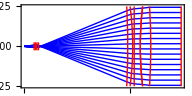
```mathematica
FullForm[-Graphics-]
```

Graphics[List[List[RGBColor[0,0,1],Line[List[List[0.,0.],List[0.0139905,-0.000738841],List[0.0161546,-0.000810446],List[0.0173693,-0.000810446],List[0.0201903,-0.000521044],List[0.145295,0.0223069],List[0.15025,0.0230679],List[0.155496,0.0234829],List[0.167135,0.0239098],List[0.167135,0.0239098],List[0.177356,0.0244278],List[0.221986,0.0244303]]],Line[List[List[0.,0.],List[0.0139905,-0.000640329],List[0.0161635,-0.000702656],List[0.0173414,-0.000702656],List[0.0201921,-0.000449383],List[0.145594,0.0192951],List[0.15104,0.0200171],List[0.155423,0.0203177],List[0.166357,0.0206659],List[0.166357,0.0206659],List[0.177764,0.0211657],List[0.221986,0.0211668]]],Line[List[List[0.,0.],List[0.0139905,-0.000541817],List[0.0161712,-0.000594751],List[0.0173175,-0.000594751],List[0.0201937,-0.000378675],List[0.145849,0.0162992],List[0.151715,0.0169552],List[0.15536,0.0171667],List[0.165701,0.0174458],List[0.165701,0.0174458],List[0.178112,0.0179051],List[0.221986,0.0179055]]],Line[List[List[0.,0.],List[0.0139905,-0.000443305],List[0.0161776,-0.000486748],List[0.0172977,-0.000486748],List[0.020195,-0.000308761],List[0.146059,0.0133169],List[0.152275,0.0138841],List[0.155308,0.0140281],List[0.165163,0.014246],List[0.165163,0.014246],List[0.178402,0.0146462],List[0.221986,0.0146463]]],Line[List[List[0.,0.],List[0.0139905,-0.000344792],List[0.0161827,-0.000378665],List[0.0172818,-0.000378665],List[0.020196,-0.000239491],List[0.146227,0.0103459],List[0.152722,0.0108058],List[0.155266,0.0108998],List[0.164738,0.0110628],List[0.164738,0.0110628],List[0.178633,0.0113891],List[0.221986,0.0113892]]],Line[List[List[0.,0.],List[0.0139905,-0.00024628],List[0.0161865,-0.000270519],List[0.0172699,-0.000270519],List[0.0201968,-0.000170715],List[0.146352,0.00738359],List[0.153056,0.00772219],List[0.155235,0.00777969],List[0.164422,0.00789269],List[0.164422,0.00789269],List[0.178806,0.00813376],List[0.221986,0.00813376]]],Line[List[List[0.,0.],List[0.0139905,-0.000147768],List[0.0161891,-0.00016233],List[0.017262,-0.00016233],List[0.0201973,-0.000102289],List[0.146435,0.00442762],List[0.153279,0.00463479],List[0.155215,0.00466544],List[0.164213,0.00473187],List[0.164213,0.00473187],List[0.178922,0.00487969],List[0.221986,0.00487969]]],Line[List[List[0.,0.],List[0.0139905,-0.0000492561],List[0.0161904,-0.0000541128],List[0.017258,-0.0000541128],List[0.0201975,-0.0000340733],List[0.146476,0.00147545],List[0.15339,0.00154517],List[0.155205,0.00155475],List[0.164108,0.00157667],List[0.164108,0.00157667],List[0.178979,0.00162647],List[0.221986,0.00162647]]],Line[List[List[0.,0.],List[0.0139905,0.0000492561],List[0.0161904,0.0000541128],List[0.017258,0.0000541128],List[0.0201975,0.0000340733],List[0.146476,-0.00147545],List[0.15339,-0.00154517],List[0.155205,-0.00155475],List[0.164108,-0.00157667],List[0.164108,-0.00157667],List[0.178979,-0.00162647],List[0.221986,-0.00162647]]],Line[List[List[0.,0.],List[0.0139905,0.000147768],List[0.0161891,0.00016233],List[0.017262,0.00016233],List[0.0201973,0.000102289],List[0.146435,-0.00442762],List[0.153279,-0.00463479],List[0.155215,-0.00466544],List[0.164213,-0.00473187],List[0.164213,-0.00473187],List[0.178922,-0.00487969],List[0.221986,-0.00487969]]],Line[List[List[0.,0.],List[0.0139905,0.00024628],List[0.0161865,0.000270519],List[0.0172699,0.000270519],List[0.0201968,0.000170715],List[0.146352,-0.00738359],List[0.153056,-0.00772219],List[0.155235,-0.00777969],List[0.164422,-0.00789269],List[0.164422,-0.00789269],List[0.178806,-0.00813376],List[0.221986,-0.00813376]]],Line[List[List[0.,0.],List[0.0139905,0.000344792],List[0.0161827,0.000378665],List[0.0172818,0.000378665],List[0.020196,0.000239491],List[0.146227,-0.0103459],List[0.152722,-0.0108058],List[0.155266,-0.0108998],List[0.164738,-0.0110628],List[0.164738,-0.0110628],List[0.178633,-0.0113891],List[0.221986,-0.0113892]]],Line[List[List[0.,0.],List[0.0139905,0.000443305],List[0.0161776,0.000486748],List[0.0172977,0.000486748],List[0.020195,0.000308761],List[0.146059,-0.0133169],List[0.152275,-0.0138841],List[0.155308,-0.0140281],List[0.165163,-0.014246],List[0.165163,-0.014246],List[0.178402,-0.0146462],List[0.221986,-0.0146463]]],Line[List[List[0.,0.],List[0.0139905,0.000541817],List[0.0161712,0.000594751],List[0.0173175,0.000594751],List[0.0201937,0.000378675],List[0.145849,-0.0162992],List[0.151715,-0.0169552],List[0.15536,-0.0171667],List[0.165701,-0.0174458],List[0.165701,-0.0174458],List[0.178112,-0.0179051],List[0.221986,-0.0179055]]],Line[List[List[0.,0.],List[0.0139905,0.000640329],List[0.0161635,0.000702656],List[0.0173414,0.000702656],List[0.0201921,0.000449383],List[0.145594,-0.0192951],List[0.15104,-0.0200171],List[0.155423,-0.0203177],List[0.166357,-0.0206659],List[0.166357,-0.0206659],List[0.177764,-0.0211657],List[0.221986,-0.0211668]]],Line[List[List[0.,0.],List[0.0139905,0.000738841],List[0.0161546,0.000810446],List[0.0173693,0.000810446],List[0.0201903,0.000521044],List[0.145295,-0.0223069],List[0.15025,-0.0230679],List[0.155496,-0.0234829],List[0.167135,-0.0239098],List[0.167135,-0.0239098],List[0.177356,-0.0244278],List[0.221986,-0.0244303]]]],List[RGBColor[1,0,0],Line[List[List[0.0139905,-0.0025],List[0.0139905,0.0025]]],Line[List[List[0.015846,-0.0025],List[0.0158732,-0.0024],List[0.0158992,-0.0023],List[0.0159242,-0.0022],List[0.015948,-0.0021],List[0.0159706,-0.002],List[0.0159922,-0.0019],List[0.0160126,-0.0018],List[0.0160319,-0.0017],List[0.0160501,-0.0016],List[0.0160671,-0.0015],List[0.0160831,-0.0014],List[0.0160979,-0.0013],List[0.0161116,-0.0012],List[0.0161242,-0.0011],List[0.0161358,-0.001],List[0.0161462,-0.0009],List[0.0161555,-0.0008],List[0.0161637,-0.0007],List[0.0161708,-0.0006],List[0.0161769,-0.0005],List[0.0161818,-0.0004],List[0.0161856,-0.0003],List[0.0161884,-0.0002],List[0.01619,-0.0001],List[0.0161905,0.],List[0.01619,0.0001],List[0.0161884,0.0002],List[0.0161856,0.0003],List[0.0161818,0.0004],List[0.0161769,0.0005],List[0.0161708,0.0006],List[0.0161637,0.0007],List[0.0161555,0.0008],List[0.0161462,0.0009],List[0.0161358,0.001],List[0.0161242,0.0011],List[0.0161116,0.0012],List[0.0160979,0.0013],List[0.0160831,0.0014],List[0.0160671,0.0015],List[0.0160501,0.0016],List[0.0160319,0.0017],List[0.0160126,0.0018],List[0.0159922,0.0019],List[0.0159706,0.002],List[0.015948,0.0021],List[0.0159242,0.0022],List[0.0158992,0.0023],List[0.0158732,0.0024],List[0.015846,0.0025]]],Line[List[List[0.0183517,-0.002475],List[0.0182625,-0.002376],List[0.0181773,-0.002277],List[0.0180961,-0.002178],List[0.0180189,-0.002079],List[0.0179457,-0.00198],List[0.0178765,-0.001881],List[0.0178112,-0.001782],List[0.0177498,-0.001683],List[0.0176923,-0.001584],List[0.0176385,-0.001485],List[0.0175885,-0.001386],List[0.0175421,-0.001287],List[0.0174994,-0.001188],List[0.0174603,-0.001089],List[0.0174248,-0.00099],List[0.0173928,-0.000891],List[0.0173642,-0.000792],List[0.0173391,-0.000693],List[0.0173174,-0.000594],List[0.017299,-0.000495],List[0.0172841,-0.000396],List[0.0172725,-0.000297],List[0.0172642,-0.000198],List[0.0172592,-0.000099],List[0.0172575,0.],List[0.0172592,0.000099],List[0.0172642,0.000198],List[0.0172725,0.000297],List[0.0172841,0.000396],List[0.017299,0.000495],List[0.0173174,0.000594],List[0.0173391,0.000693],List[0.0173642,0.000792],List[0.0173928,0.000891],List[0.0174248,0.00099],List[0.0174603,0.001089],List[0.0174994,0.001188],List[0.0175421,0.001287],List[0.0175885,0.001386],List[0.0176385,0.001485],List[0.0176923,0.001584],List[0.0177498,0.001683],List[0.0178112,0.001782],List[0.0178765,0.001881],List[0.0179457,0.00198],List[0.0180189,0.002079],List[0.0180961,0.002178],List[0.0181773,0.002277],List[0.0182625,0.002376],List[0.0183517,0.002475]]],Line[List[List[0.0200333,-0.002475],List[0.0200462,-0.002376],List[0.0200586,-0.002277],List[0.0200705,-0.002178],List[0.0200818,-0.002079],List[0.0200926,-0.00198],List[0.0201028,-0.001881],List[0.0201126,-0.001782],List[0.0201218,-0.001683],List[0.0201304,-0.001584],List[0.0201386,-0.001485],List[0.0201462,-0.001386],List[0.0201533,-0.001287],List[0.0201598,-0.001188],List[0.0201659,-0.001089],List[0.0201714,-0.00099],List[0.0201763,-0.000891],List[0.0201808,-0.000792],List[0.0201847,-0.000693],List[0.0201881,-0.000594],List[0.020191,-0.000495],List[0.0201934,-0.000396],List[0.0201952,-0.000297],List[0.0201965,-0.000198],List[0.0201973,-0.000099],List[0.0201975,0.],List[0.0201973,0.000099],List[0.0201965,0.000198],List[0.0201952,0.000297],List[0.0201934,0.000396],List[0.020191,0.000495],List[0.0201881,0.000594],List[0.0201847,0.000693],List[0.0201808,0.000792],List[0.0201763,0.000891],List[0.0201714,0.00099],List[0.0201659,0.001089],List[0.0201598,0.001188],List[0.0201533,0.001287],List[0.0201462,0.001386],List[0.0201386,0.001485],List[0.0201304,0.001584],List[0.0201218,0.001683],List[0.0201126,0.001782],List[0.0201028,0.001881],List[0.0200926,0.00198],List[0.0200818,0.002079],List[0.0200705,0.002178],List[0.0200586,0.002277],List[0.0200462,0.002376],List[0.0200333,0.002475]]],Circle[List[-0.0637834,0],0.210265,List[-0.11918,0.11918]],Circle[List[0.0674486,0],0.085955,List[-0.295115,0.295115]],Circle[List[1.09645,0],0.94125,List[3.11503,3.16816]],Circle[List[0.259645,0],0.09555,List[2.87687,3.40632]],Circle[List[0.259645,0],0.09555,List[2.87687,3.40632]],Circle[List[-0.00486873,0],0.183855,List[-0.136399,0.136399]],Line[List[List[0.221986,Rational[-1,40]],List[0.221986,Rational[1,40]]]]]],Rule[AspectRatio,Rational[1,2]],Rule[Frame,True],Rule[ImageSize,List[192.5,Automatic]],Rule[PlotRange,List[List[0,All],List[Rational[-3,100],Rational[3,100]]]],Rule[PlotRangeClipping,True]]

```mathematica
?Cases
```

Cases[{e_1,e_2,…},pattern] gives a list of the e_i that match the pattern. 
Cases[{e_1,…},pattern→rhs] gives a list of the values of rhs corresponding to the e_i that match the pattern. 
Cases[expr,pattern,levelspec] gives a list of all parts of expr on levels specified by levelspec that match the pattern. 
Cases[expr,pattern→rhs,levelspec] gives the values of rhs that match the pattern. 
Cases[expr,pattern,levelspec,n] gives the first n parts in expr that match the pattern. 
Cases[pattern] represents an operator form of Cases that can be applied to an expression.

```mathematica
ListPlot[data]
```

-Graphics-

## Beam Divergence

This section plots the data we obtained in measuring the collimated beam from the Raman optics. This was done to check that the divergence angle was sufficiently small so that it did not significantly contribute to a loss in fringe contrast.

The data were obtained by imaging the beam on a piece of paper. The camera and the paper were mounted on a track and moved along the optic axis. Previous calibration of the camera gives a pixel size of 5.1px/mm.

```mathematica
beamImages =Import[#]&/@FileNames["PlotData/Raman_Beam_Divergence/*"];
beamImages=Map[Mean,ImageData[#],{2}]&/@beamImages;
```

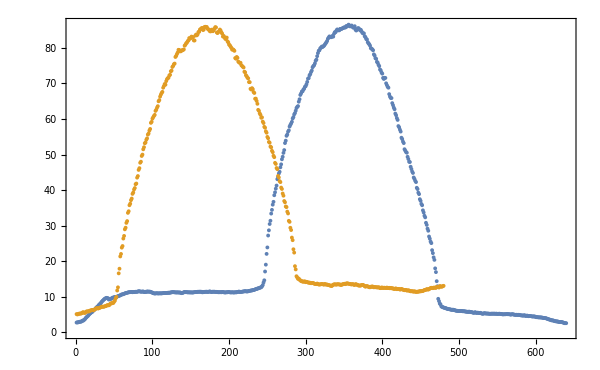

```mathematica
ListPlot[{Total@#,Total@Transpose[#]}&[beamImages⟦1⟧]]
```

To fit to this, we know that the intensity of the beam is described by a Gaussian. However, the beam is also apetured by the lens. A proper measurement of the background was not taken, but since the intensity of the beam was high, I will assume that the signal/noise ratio is also high and take the background to be zero.

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True. 
Select[crit] represents an operator form of Select that can be applied to an expression.

```mathematica
gaussFit[ data_,thresh_:50]:=Module[{truncData=Select[Transpose[{Range[Length[data]],data}],#⟦2⟧>thresh&],nlm},
nlm=NonlinearModelFit[truncData,A Exp[-(2(x-μ)^2)/σ^2],{{A,Max[truncData⟦All,2⟧]},{μ,Position[truncData⟦All,2⟧,Max[truncData⟦All,2⟧]]⟦1,1⟧},{σ,100}},x,VarianceEstimatorFunction->(1&),Weights->1/truncData⟦All,2⟧^2];
nlm
]
```

```mathematica
gaussFromBeamData[beamData_,thresh_:50]:=Module[{Xfit=gaussFit[Total@beamData,thresh],Yfit=gaussFit[Total@Transpose[beamData],thresh]},
Transpose[{{μ,σ}/.#["BestFitParameters"],#["ParameterErrors"]⟦{2,3}⟧}]&/@{Xfit,Yfit}
]
```

```mathematica
getWidths[fitVals_]:=fitVals⟦All,2⟧
```

```mathematica
?Most
```

Most[expr] gives expr with the last element removed.

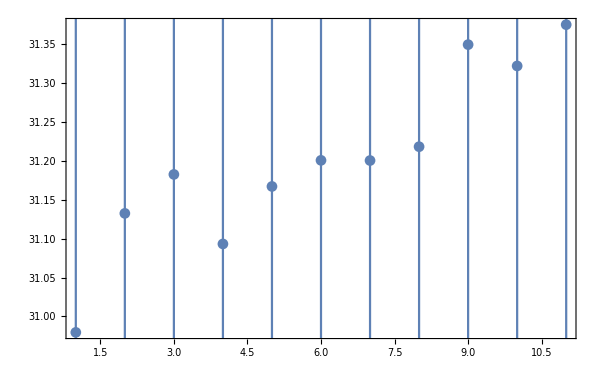

```mathematica
ErrorListPlot[1/5.1 Most[gaussFromBeamData[beamImages⟦#⟧,50]⟦All,2⟧⟦1⟧&/@Range[Length[beamImages]]],PlotRange->All]
```

```mathematica
?LinearModelFit
```

LinearModelFit[{y_1,y_2,…},{f_1,f_2,…},x] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… that fits the y_i for successive x values 1, 2, ….
LinearModelFit[{{x_11,x_12,…,y_1},{x_21,x_22,…,y_2},…},{f_1,f_2,…},{x_1,x_2,…}] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… where the f_i depend on the variables x_k. 
LinearModelFit[{m,v}] constructs a linear model from the design matrix m and response vector v.

```mathematica
LinearModelFit[#⟦All,1⟧,x,x]&[Most[gaussFromBeamData[beamImages⟦#⟧,50]⟦All,2⟧⟦2⟧&/@Range[Length[beamImages]]]]
```

FittedModel[83.7245+0.0203039 x]

```mathematica
gaussFit[Total@beamImages⟦2⟧,50]["BestFitParameters"]
```

{A→86.7454,μ→349.57,σ→79.388}

```mathematica
gaussFit[Total@beamImages⟦2⟧,50]["ParameterErrors"]⟦{2,3}⟧
```

{10.5904,20.0175}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

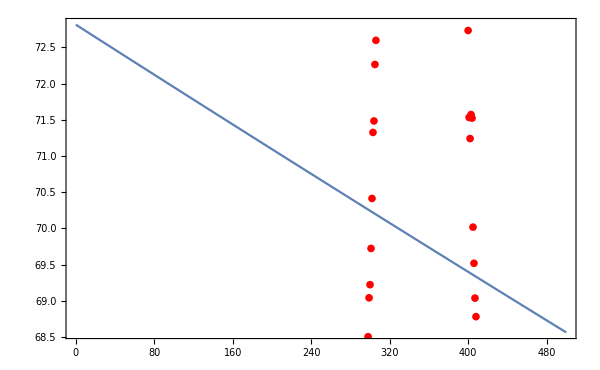

```mathematica
Show[Plot[Evaluate[gaussFit[Total@beamImages⟦1⟧,50][x]],{x,0,500}],ListPlot[gaussFit[Total@beamImages⟦1⟧,50]["Data"],PlotStyle->Red]]
```

## Waveplate Thickness

```mathematica
plateFile = Import["PlotData/waveplate.csv","CSV"];
```

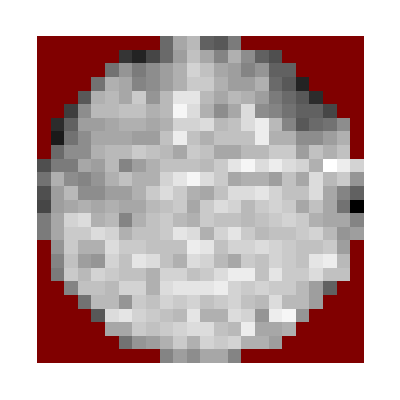

```mathematica
ArrayPlot[plateFile]
```

Find the mean of all values not 0

```mathematica
meanVal=Mean[Select[Flatten[plateFile],#≠0&]];
```

```mathematica
N[3994/447]
```

8.93512

```mathematica
?NumericQ
```

NumericQ[expr] gives True if expr is a numeric quantity, and False otherwise.

## Mirror Mount

The mirror mount was aligned using a stepper motor, which has an angular displacement per step of 0.9°. The thumbscrew this rotates has a pitch which causes the mirror to move by 250 μm/turn. In terms of steps, this corresponds to a distance of 0.625 μm. The mount pivots about a point which is 34.5mm away from the thumbscrew. For small angles, displacing the screw by by 0.625 μm tilts the mirror by 18.1 μRad

```mathematica
ArcTan[0.625/34500] 10^6
```

18.1159

Let’s assume the piezo stack length varies linearly with the applied voltage. The full extension is 23 μm over 150 V.  As an angle, this corresponds to 666 μRad, or ~66 μRad per unit of control voltage.

```mathematica
ArcTan[23./34500] 10^6
```

666.667

```mathematica
666./150
```

The optimum is about 0.2 V away from the maximum, which corresponds to an angular displacement of 13 μRad

```mathematica
66./5
```

13.2

```mathematica
opticsC230260PTripletReversedNoAsphere[d0_, d1_, d2_]:=Flatten[{
 AirSpacedTriplet[R1,R2,R3,R4,R5,R6,TC1,TC2,TC3,gap1,gap2,N1,N2,N3,Dia][ d2]/.Reversed[lens3],
  Interface[∞, d0 + (TC1/.lens4) + 1.067mm + (TC1/.lens5) + d1 + (TC1+TC2+TC3+gap1+gap2/.lens3) + d2, 1, 25mm]}];
```

```mathematica
opticsC230260PTripletReversed[d0_, d1_, d2_]:=Flatten[{
Aspheric[{R1,k1,A4,A6,A8,A10,A12,A14,A16},{R2,k2,B4,B6,B8,B10,B12,B14,B16},TC1,N1,Dia][      1.067mm + (TC1/.lens5) + d1 + (TC1+TC2+TC3+gap1+gap2/.lens3) + d2]/.Reversed[lens4],
  Aspheric[{R1,k1,A4,A6,A8,A10,A12,A14,A16},{R2,k2,B4,B6,B8,B10,B12,B14,B16},TC1,N1,Dia][   d1 + (TC1+TC2+TC3+gap1+gap2/.lens3) + d2]/.Reversed[lens5],
 AirSpacedTriplet[R1,R2,R3,R4,R5,R6,TC1,TC2,TC3,gap1,gap2,N1,N2,N3,Dia][ d2]/.Reversed[lens3],
  Interface[∞, d0 + (TC1/.lens4) + 1.067mm + (TC1/.lens5) + d1 + (TC1+TC2+TC3+gap1+gap2/.lens3) + d2, 1, 25mm]}];
```

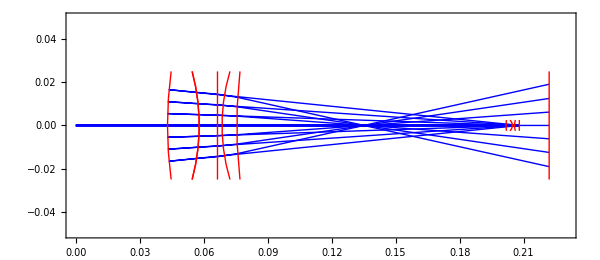

```mathematica
Block[{d0=pC230260P,
           d1=frontFocusTriplet +qC230260P,
           d2=43mm},
optics =opticsC230260PTripletReversed[d0,d1,d2];
bundle=Table[Ray[0,y,0,1],{y,-0.02,0.02,0.04/400}];
g={RayPathGraphics[optics][bundle],InterfaceGraphics[optics]};
Show[g,PlotRange->{{0,0.23},{-50mm,50mm}},PlotRangeClipping->True,Frame->True,AspectRatio->Automatic,ImageSize->600, FrameLabel->{"Test"}]]
```

Approximating each lens as a thin lens, using the front focal lengths, the spot size at the fibre is 3mm!!

```mathematica
reverseTrain := Train[Lens[f,f],Translation[d1,1],Lens[f2,f2],Translation[1.067mm],Lens[f1,f1],Translation[d0]];
qReverse = Transform[reverseTrain][qWaist[44mm,0,λ]]//Simplify;
```

```mathematica
10^6 SpotSize[qReverse,λ]/.{f1->13.99mm, f2->4.26mm,f->123.5mm, d0->15.37mm,d1->127mm+2.9mm,ω0->2.4µm, λ->780nm}
```

2956.91

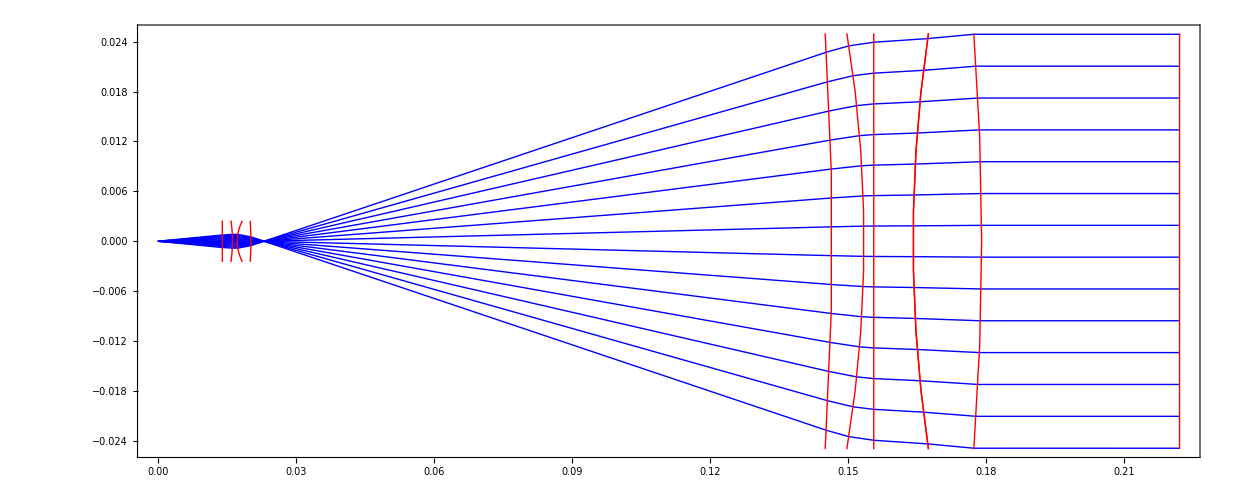

Now if we suppose the reflected rays are tilted by this angle, at what distance from the original focus does this spot form? This can be calculated using Malcolm’s ray tracer

```mathematica
Export["PlotData/waveplate_avg.csv",N[Map[If[#≠0,#-meanVal,Null]&,plateFile,{2}]]]
```